```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];  (* already have Repeating or Dead Verdict *)

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]
(* ,DistanceLastPositions[sss],DistanceTally[sss]  *) },
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]
(* ,DistanceLastPositions[sss],DistanceTally[sss] *)  },
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss; Print[vdct]]; (* update it if changed *)
ans
];
```

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

original functions:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
sss50=SSS[50,50,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];
sss90=SSS[90,20,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];$debug=False;
```

```mathematica
$debug=False;
sss50⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]==sss50⟦"Net"⟧
```

Note the ambiguity here!  A different reduced form for this network would be:

```mathematica
{11·{{},{1,2,3}},{},{}},2·{{}},1·{{1,2,3}}
```

In fact, for doing the “offset and subtract” step, to identify dimension, the original, unreduced version is fine.  This is always true for 1-d networks, the reduced version becomes necessary for higher dimensions.

```mathematica
sss90⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]==sss90⟦"Net"⟧
```

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
nds=ToNetDifferenceSets[sss50⟦"Net"⟧]
```

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

Here an offset by 4 results in lots of 0s:

```mathematica
SetSubtract[nds⟦5;;-1⟧,nds⟦1;;-5⟧]
```

{{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0}}

```mathematica
nds=ToNetDifferenceSets[sss90⟦"Net"⟧]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
SetSubtract[nds⟦2;;-1⟧,nds⟦1;;-2⟧]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
RecognizeNetSetDifferenceRow@ToNetDifferenceSets[sss90["Net"]]
```

{dim,{1,0,{1}}}

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

#### stuff

```mathematica
ssst0=SSS[{"AB"->"BAA",""->"ABAA"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

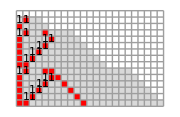

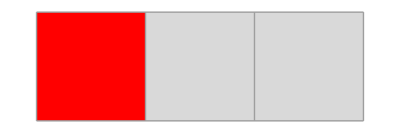
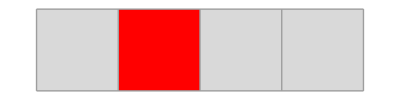
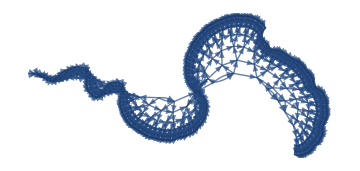
#### " "-Graphics- -Graphics- | "→" | -Graphics- -Graphics- | "→" | -Graphics-"Substitution Rules:"-Graphics-

```mathematica
{{"exp",{1,0,5,2},{{1}, {2}, {4}},{{1, 3, 9, 23, 53, 115, 241, 495}, {2, 6, 14, 30, 62, 126, 254, }, {4, 8, 16, 32, 64, 128, , }}},{"exp",{1,0,4,2},{{3}, {6}, {8}},{{3, 9, 23, 53, 115, 241, 495}, {6, 14, 30, 62, 126, 254, }, {8, 16, 32, 64, 128, , }}},{"failed"},{"failed"}}
```

{{1,1},{3},{1,1,2,3},{3,4,7},3·{{1}},{7},{1,1,2,3},{3,4,15},{1,4,5},{1,5,6},{1,6,7},{7,8,15},7·{{1}},{15},{1,1,2,3},{3,4,31},{1,4,5},{1,5,6},{1,6,7},{7,8,31},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,31},15·{{1}},{31},{1,1,2,3},{3,4,63},{1,4,5},{1,5,6},{1,6,7},{7,8,63},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,63},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32,63},31·{{1}},{63},{1,1,2,3},{3,4,127},{1,4,5},{1,5,6},{1,6,7},{7,8,127},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,127},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32,127},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{63,64,127},63·{{1}},{127},{1,1,2,3},{3,4,255},{1,4,5},{1,5,6},{1,6,7},{7,8,255},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,255},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32,255},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{63,64,255},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{127,128,255},127·{{1}},{255},{1,1,2,3},{3,4},{1,4,5},{1,5,6},{1,6,7},{7,8},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{63,64},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{127,128},{1,128,129},126·{{1}},{},{1}}

#### SequenceForm[Association["Index" -> 50468705, "QCode" -> "34243333143", "RuleSet" -> {"AB" -> "BAAAA", "" -> "BA"}], " : ", {"failed", "exp2", "exp3", "failed"}, " - ", "OK"]

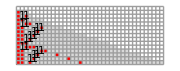
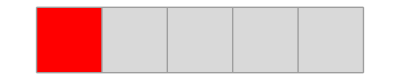

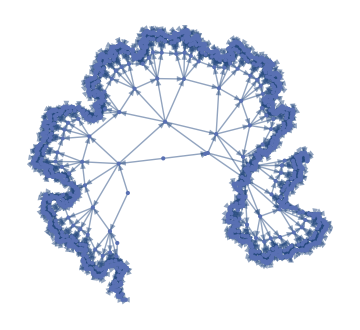
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssst0=SSS[{"AB"->"BAAAA",""->"BA"},"",1500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

```mathematica
{{"failed",{{2, 4, 10, 32, 118, 460}, {2, 6, 22, 86, 342, }, {4, 16, 64, 256, , }}},{"failed",{{2, 4, 10, 32, 118, 460}, {2, 6, 22, 86, 342, }, {4, 16, 64, 256, , }}},{"failed"},{"failed",{{2, 7, 19, 41, 127, 462}, {5, 12, 22, 86, 335, }, {7, 10, 64, 249, , }}}}
```

{{2},{1,3},{3},{1,7},{1,2,3,4,7},3·{{1}},{7},{1,23},{1,2,3,4,23},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,23},15·{{1}},{23},{1,87},{1,2,3,4,87},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,87},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64,87},63·{{1}},{87},{1,343},{1,2,3,4,343},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,343},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64,343},{1,64,65,66,67},{1,67,68,69,70},{1,70,71,72,73},{1,73,74,75,76},{1,76,77,78,79},{1,79,80,81,82},{1,82,83,84,85},{1,85,86,87,88},{1,88,89,90,91},{1,91,92,93,94},{1,94,95,96,97},{1,97,98,99,100},{1,100,101,102,103},{1,103,104,105,106},{1,106,107,108,109},{1,109,110,111,112},{1,112,113,114,115},{1,115,116,117,118},{1,118,119,120,121},{1,121,122,123,124},{1,124,125,126,127},{1,127,128,129,130},{1,130,131,132,133},{1,133,134,135,136},{1,136,137,138,139},{1,139,140,141,142},{1,142,143,144,145},{1,145,146,147,148},{1,148,149,150,151},{1,151,152,153,154},{1,154,155,156,157},{1,157,158,159,160},{1,160,161,162,163},{1,163,164,165,166},{1,166,167,168,169},{1,169,170,171,172},{1,172,173,174,175},{1,175,176,177,178},{1,178,179,180,181},{1,181,182,183,184},{1,184,185,186,187},{1,187,188,189,190},{1,190,191,192,193},{1,193,194,195,196},{1,196,197,198,199},{1,199,200,201,202},{1,202,203,204,205},{1,205,206,207,208},{1,208,209,210,211},{1,211,212,213,214},{1,214,215,216,217},{1,217,218,219,220},{1,220,221,222,223},{1,223,224,225,226},{1,226,227,228,229},{1,229,230,231,232},{1,232,233,234,235},{1,235,236,237,238},{1,238,239,240,241},{1,241,242,243,244},{1,244,245,246,247},{1,247,248,249,250},{1,250,251,252,253},{253,254,255,256,343},255·{{1}},{343},{1},{1,2,3,4},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64},{1,64,65,66,67},{1,67,68,69,70},{1,70,71,72,73},{1,73,74,75,76},{1,76,77,78,79},{1,79,80,81,82},{1,82,83,84,85},{1,85,86,87,88},{1,88,89,90,91},{1,91,92,93,94},{1,94,95,96,97},{1,97,98,99,100},{1,100,101,102,103},{1,103,104,105,106},{1,106,107,108,109},{1,109,110,111,112},{1,112,113,114,115},{1,115,116,117,118},{1,118,119,120,121},{1,121,122,123,124},{1,124,125,126,127},{1,127,128,129,130},{1,130,131,132,133},{1,133,134,135,136},{1,136,137,138,139},{1,139,140,141,142},{1,142,143,144,145},{1,145,146,147,148},{1,148,149,150,151},{1,151,152,153,154},{1,154,155,156,157},{1,157,158,159,160},{1,160,161,162,163},{1,163,164,165,166},{1,166,167,168,169},{1,169,170,171,172},{1,172,173,174,175},{1,175,176,177,178},{1,178,179,180,181},{1,181,182,183,184},{1,184,185,186,187},{1,187,188,189,190},{1,190,191,192,193},{1,193,194,195,196},{1,196,197,198,199},{1,199,200,201,202},{1,202,203,204,205},{1,205,206,207,208},{1,208,209,210,211},{1,211,212,213,214},{1,214,215,216,217},{1,217,218,219,220},{1,220,221,222,223},{1,223,224,225,226},{1,226,227,228,229},{1,229,230,231,232},{1,232,233,234,235},{1,235,236,237,238},{1,238,239,240,241},{1,241,242,243,244},{1,244,245,246,247},{1,247,248,249,250},{1,250,251,252,253},{253,254,255,256},{1,256,257,258,259},{1,259,260,261,262},{1,262,263,264,265},{1,265,266,267,268},{1,268,269,270,271},{1,271,272,273,274},{1,274,275,276,277},{1,277,278,279,280},{1,280,281,282,283},{1,283,284,285,286},{1,286,287,288,289},{1,289,290,291,292},{1,292,293,294,295},{1,295,296,297,298},{1,298,299,300,301},{1,301,302,303,304},{1,304,305,306,307},{1,307,308,309,310},{1,310,311,312,313},{1,313,314,315,316},{1,316,317,318,319},{1,319,320,321,322},{1,322,323,324,325},{1,325,326,327,328},{1,328,329,330,331},{1,331,332,333,334},{1,334,335,336,337},{1,337,338,339,340},{1,340,341,342,343},{1,343,344,345,346},{1,346,347,348,349},{1,349,350,351,352},{1,352,353,354,355},{1,355,356,357,358},{1,358,359,360,361},{1,361,362,363,364},{1,364,365,366,367},{1,367,368,369,370},{1,370,371,372,373},{1,373,374,375,376},{1,376,377,378,379},{1,379,380,381,382},{1,382,383,384,385},{1,385,386,387,388},{1,388,389,390,391},{1,391,392,393,394},{1,394,395,396,397},{1,397,398,399,400},{1,400,401,402,403},{1,403,404,405,406},{1,406,407,408,409},{1,409,410,411,412},{1,412,413,414,415},{1,415,416,417,418},{1,418,419,420,421},{1,421,422,423,424},{1,424,425,426,427},{1,427,428,429,430},{1,430,431,432,433},{1,433,434,435,436},{1,436,437,438,439},{1,439,440,441,442},{1,442,443,444,445},{1,445,446,447,448},{1,448,449,450,451},{1,451,452,453,454},{1,454,455,456,457},{1,457,458,459,460},{1,460,461,462,463},{1,463,464,465,466},{1,466,467,468,469},{1,469,470,471,472},{1,472,473,474,475},{1,475,476,477,478},{1,478,479,480,481},{1,481,482,483,484},{1,484,485,486,487},{1,487,488,489,490},{1,490,491,492,493},{1,493,494,495,496},{1,496,497,498,499},{1,499,500,501,502},{1,502,503,504,505},{1,505,506,507,508},{1,508,509,510,511},{1,511,512,513,514},{1,514,515,516,517},{1,517,518,519,520},{1,520,521,522,523},{1,523,524,525,526},{1,526,527,528,529},{1,529,530,531,532},{1,532,533,534,535},{1,535,536,537,538},{1,538,539,540,541},{1,541,542,543,544},{1,544,545,546,547},{1,547,548,549,550},{1,550,551,552,553},{1,553,554,555,556},{1,556,557,558,559},{1,559,560,561,562},{1,562,563,564,565},{1,565,566,567,568},{1,568,569,570,571},{1,571,572,573,574},{1,574,575,576,577},{1,577,578,579,580},{1,580,581,582,583},{1,583,584,585,586},{1,586,587,588,589},{1,589,590,591,592},{1,592,593,594,595},{1,595,596,597,598},{1,598,599,600,601},{1,601,602,603,604},{1,604,605,606,607},{1,607,608,609,610},{1,610,611,612,613},{1,613,614,615,616},{1,616,617,618,619},{1,619,620,621,622},{1,622,623,624,625},{1,625,626,627,628},{1,628,629,630,631},{1,631,632,633,634},{1,634,635,636,637},{1,637,638,639,640},{1,640,641,642,643},{1,643,644,645,646},{1,646,647,648,649},{1,649,650,651,652},{1,652,653,654,655},{1,655,656,657,658},{1,658,659,660,661},{1,661,662,663,664},{1,664,665,666,667},{1,667,668,669,670},{1,670,671,672,673},{1,673,674,675,676},{1,676,677,678,679},{1,679,680,681,682},{1,682,683,684,685},{1,685,686,687,688},{1,688,689,690,691},{1,691,692,693,694},{1,694,695,696,697},{1,697,698,699,700},{1,700,701,702,703},{1,703,704,705,706},{1,706,707,708,709},{1,709,710,711,712},{1,712,713,714,715},{1,715,716,717,718},{1,718,719,720,721},{1,721,722,723,724},{1,724,725,726,727},{1,727,728,729,730},{1,730,731,732,733},{1,733,734,735,736},{1,736,737,738,739},{1,739,740,741,742},{1,742,743,744,745},{1,745,746,747,748},{1,748,749,750,751},{1,751,752,753,754},{1,754,755,756,757},{1,757,758,759,760},{1,760,761,762,763},{1,763,764,765,766},{1,766,767,768,769},{1,769,770,771,772},{1,772,773,774,775},{1,775,776,777,778},{1,778,779,780},80·{{1}},{},698·{{1}}}

#### SequenceForm[Association["Index" -> 251949890, "QCode" -> "342333232413", "RuleSet" -> {"AB" -> "AAAA", "AA" -> "B", "" -> "AA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

```mathematica
ssst0=SSS[{"AB"->"AAAA","AA"->"B",""->"AA"},"",1500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

$Aborted

{{failed,2 | 4 | 10 | 32 | 118 | 460
2 | 6 | 22 | 86 | 342 | 
4 | 16 | 64 | 256 |  | },{failed,2 | 4 | 10 | 32 | 118 | 460
2 | 6 | 22 | 86 | 342 | 
4 | 16 | 64 | 256 |  | },{exp,{3,0,3,2},1 | 2 | 4
1 | 2 | 2
1 | 0 | 2
-1 | 2 | 0,1 | 2 | 4 | 6 | 10 | 16 | 24 | 38 | 62 | 92 | 148 | 242
1 | 2 | 2 | 4 | 6 | 8 | 14 | 24 | 30 | 56 | 94 | 
1 | 0 | 2 | 2 | 2 | 6 | 10 | 6 | 26 | 38 |  | 
-1 | 2 | 0 | 0 | 4 | 4 | -4 | 20 | 12 |  |  | },{failed,2 | 7 | 19 | 41 | 127 | 462
5 | 12 | 22 | 86 | 335 | 
7 | 10 | 64 | 249 |  | }}

{{2},{1,3},{3},{1,7},{1,2,3,4,7},3·{{1}},{7},{1,23},{1,2,3,4,23},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,23},15·{{1}},{23},{1,87},{1,2,3,4,87},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,87},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64,87},63·{{1}},{87},{1,343},{1,2,3,4,343},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16,343},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64,343},{1,64,65,66,67},{1,67,68,69,70},{1,70,71,72,73},{1,73,74,75,76},{1,76,77,78,79},{1,79,80,81,82},{1,82,83,84,85},{1,85,86,87,88},{1,88,89,90,91},{1,91,92,93,94},{1,94,95,96,97},{1,97,98,99,100},{1,100,101,102,103},{1,103,104,105,106},{1,106,107,108,109},{1,109,110,111,112},{1,112,113,114,115},{1,115,116,117,118},{1,118,119,120,121},{1,121,122,123,124},{1,124,125,126,127},{1,127,128,129,130},{1,130,131,132,133},{1,133,134,135,136},{1,136,137,138,139},{1,139,140,141,142},{1,142,143,144,145},{1,145,146,147,148},{1,148,149,150,151},{1,151,152,153,154},{1,154,155,156,157},{1,157,158,159,160},{1,160,161,162,163},{1,163,164,165,166},{1,166,167,168,169},{1,169,170,171,172},{1,172,173,174,175},{1,175,176,177,178},{1,178,179,180,181},{1,181,182,183,184},{1,184,185,186,187},{1,187,188,189,190},{1,190,191,192,193},{1,193,194,195,196},{1,196,197,198,199},{1,199,200,201,202},{1,202,203,204,205},{1,205,206,207,208},{1,208,209,210,211},{1,211,212,213,214},{1,214,215,216,217},{1,217,218,219,220},{1,220,221,222,223},{1,223,224,225,226},{1,226,227,228,229},{1,229,230,231,232},{1,232,233,234,235},{1,235,236,237,238},{1,238,239,240,241},{1,241,242,243,244},{1,244,245,246,247},{1,247,248,249,250},{1,250,251,252,253},{253,254,255,256,343},255·{{1}},{},{1},{1,2,3,4},{1,4,5,6,7},{1,7,8,9,10},{1,10,11,12,13},{13,14,15,16},{1,16,17,18,19},{1,19,20,21,22},{1,22,23,24,25},{1,25,26,27,28},{1,28,29,30,31},{1,31,32,33,34},{1,34,35,36,37},{1,37,38,39,40},{1,40,41,42,43},{1,43,44,45,46},{1,46,47,48,49},{1,49,50,51,52},{1,52,53,54,55},{1,55,56,57,58},{1,58,59,60,61},{61,62,63,64},{1,64,65,66,67},{1,67,68,69,70},{1,70,71,72,73},{1,73,74,75,76},{1,76,77,78,79},{1,79,80,81,82},{1,82,83,84,85},{1,85,86,87,88},{1,88,89,90,91},{1,91,92,93,94},{1,94,95,96,97},{1,97,98,99,100},{1,100,101,102,103},{1,103,104,105,106},{1,106,107,108,109},{1,109,110,111,112},{1,112,113,114,115},{1,115,116,117,118},{1,118,119,120,121},{1,121,122,123,124},{1,124,125,126,127},{1,127,128,129,130},{1,130,131,132,133},{1,133,134,135,136},{1,136,137,138,139},{1,139,140,141,142},{1,142,143,144,145},{1,145,146,147,148},{1,148,149,150,151},{1,151,152,153,154},{1,154,155,156,157},{1,157,158,159,160},{1,160,161,162,163},{1,163,164,165,166},{1,166,167,168,169},{1,169,170,171,172},{1,172,173,174,175},{1,175,176,177,178},{1,178,179,180,181},{1,181,182,183,184},{1,184,185,186,187},{1,187,188,189,190},{1,190,191,192,193},{1,193,194,195,196},{1,196,197,198,199},{1,199,200,201,202},{1,202,203,204,205},{1,205,206,207,208},{1,208,209,210,211},{1,211,212,213,214},{1,214,215,216,217},{1,217},11·{{1}},{},204·{{1}}}

#### SequenceForm[Association["Index" -> 1181262450, "QCode" -> "3243234233133", "RuleSet" -> {"AA" -> "BA", "AB" -> "AAA", "" -> "AAA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

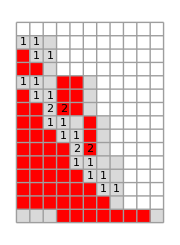
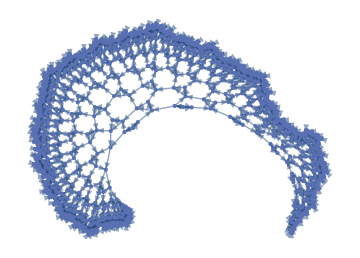
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2},{1,5},{7,10},{1,1,2},{1,12},{1,14},{1,1,2},{1,15},{1,17},{1,1,2},{1,18},{1,20},{22,25},{1,1,2},{1,27},{1,29},{1,1,2},{1,30},{1,32},{1,1,2},{1,33},{1,35},{1,1,2},{1,36},{1,38},{1,1,2},{1,39},{1,41},{1,1,2},{1,42},{1,44},{1,1,2},{1,45},{1,47},{1,1,2},{1,48},{1,50},{52,55},{1,1,2},{1,57},{1,59},{1,1,2},{1,60},{1,62},{1,1,2},{1,63},{1,65},{1,1,2},{1,66},{1,68},{1,1,2},{1,69},{1,71},{1,1,2},{1,72},{1,74},{1,1,2},{1,75},{1,77},{1,1,2},{1,78},{1,80},{1,1,2},{1,81},{1,83},{1,1,2},{1,84},{1,86},{1,1,2},{1,87},{1,89},{1,1,2},{1,90},{1,92},{1,1,2},{1,93},{1,95},{1,1,2},{1,96},{1,98},{1,1,2},{1,99},{1,101},{1,1,2},{1,102},{1,104},{1,1,2},{1,105},{1,107},{1,1,2},{1,108},{1,110},{112,115},{1,1,2},{1,117},{1,119},{1,1,2},{1,120},{1,122},{1,1,2},{1,123},{1,125},{1,1,2},{1,126},{1,128},{1,1,2},{1,129},{1,131},{1,1,2},{1,132},{1,134},{1,1,2},{1,135},{1,137},{1,1,2},{1,138},{1,140},{1,1,2},{1,141},{1,143},{1,1,2},{1,144},{1,146},{1,1,2},{1,147},{1,149},{1,1,2},{1,150},{1,152},{1,1,2},{1,153},{1,155},{1,1,2},{1,156},{1,158},{1,1,2},{1,159},{1,161},{1,1,2},{1,162},{1,164},{1,1,2},{1,165},{1,167},{1,1,2},{1,168},{1,170},{1,1,2},{1,171},{1,173},{1,1,2},{1,174},{1,176},{1,1,2},{1,177},{1,179},{1,1,2},{1,180},{1,182},{1,1,2},{1,183},{1,185},{1,1,2},{1,186},{1,188},{1,1,2},{1,189},{1,191},{1,1,2},{1,192},{1,194},{1,1,2},{1,195},{1,197},{1,1,2},{1,198},{1,200},{1,1,2},{1,201},{1,203},{1,1,2},{1,204},{1,206},{1,1,2},{1,207},{1,209},{1,1,2},{1,210},{1,212},{1,1,2},{1,213},{1,215},{1,1,2},{1,216},{1,218},{1,1,2},{1,219},{1,221},{1,1,2},{1,222},{1,224},{1,1,2},{1,225},{1,227},{1,1,2},{1,228},{1,230},{232,235},{1,1,2},{1,237},{1,239},{1,1,2},{1,240},{1,242},{1,1,2},{1,243},{1,245},{1,1,2},{1,246},{1,248},{1,1,2},{1,249},{1,251},{1,1,2},{1,252},{1,254},{1,1,2},{1,255},{1,257},{1,1,2},{1,258},{1,260},{1,1,2},{1,261},{1,263},{1,1,2},{1,264},{1,266},{1,1,2},{1,267},{1,269},{1,1,2},{1,270},{1,272},{1,1,2},{1,273},{1,275},{1,1,2},{1,276},{1,278},{1,1,2},{1,279},{1,281},{1,1,2},{1,282},{1,284},{1,1,2},{1,285},{1,287},{1,1,2},{1,288},{1,290},{1,1,2},{1,291},{1,293},{1,1,2},{1,294},{1,296},{1,1,2},{1,297},{1,299},{1,1,2},{1,300},{1,302},{1,1,2},{1,303},{1,305},{1,1,2},{1,306},{1,308},{1,1,2},{1,309},{1,311},{1,1,2},{1,312},{1,314},{1,1,2},{1,315},{1,317},{1,1,2},{1,318},{1,320},{1,1,2},{1,321},{1,323},{1,1,2},{1,324},{1,326},{1,1,2},{1,327},{1,329},{1,1,2},{1,330},{1,332},{1,1,2},{1,333},{1,335},{1,1,2},{1,336},{1,338},{1,1,2},{1,339},{1,341},{1,1,2},{1,342},{1,344},{1,1,2},{1,345},{1,347},{1,1,2},{1,348},{1,350},{1,1,2},{1,351},{1,353},{1,1,2},{1,354},{1,356},{1,1,2},{1,357},{1,359},{1,1,2},{1,360},{1,362},{1,1,2},{1,363},{1,365},{1,1,2},{1,366},{1,368},{1,1,2},{1,369},{1,371},{1,1,2},{1,372},{1,374},{1,1,2},{1,375},{1,377},{1,1,2},{1,378},{1,380},{1,1,2},{1,381},{1,383},{1,1,2},{1,384},{1,386},{1,1,2},{1,387},{1,389},{1,1,2},{1,390},{1,392},{1,1,2},{1,393},{1,395},{1,1,2},{1,396},{1,398},{1,1,2},{1,399},{1,401},{1,1,2},{1,402},{1,404},{1,1,2},{1,405},{1,407},{1,1,2},{1,408},{1,410},{1,1,2},{1,411},{1,413},{1,1,2},{1,414},{1,416},{1,1,2},{1,417},{1,419},{1,1,2},{1,420},{1,422},{1,1,2},{1,423},{1,425},{1,1,2},{1,426},{1,428},{1,1,2},{1,429},{1,431},{1,1,2},{1,432},{1,434},{1,1,2},{1,435},{1,437},{1,1,2},{1,438},{1,440},{1,1,2},{1,441},{1,443},{1,1,2},{1,444},{1,446},{1,1,2},{1,447},{1,449},{1,1,2},{1,450},{1,452},{1,1,2},{1,453},{1,455},{1,1,2},{1,456},{1,458},{1,1,2},{1,459},{1,461},{1,1,2},{1,462},{1,464},{1,1,2},{1,465},{1,467},{1,1,2},{1,468},{1,470},{472,475},{1,1,2},{1,477},{1,479},{1,1,2},{1,480},{1,482},{1,1,2},{1,483},{1,485},{1,1,2},{1,486},{1,488},{1,1,2},{1,489},{1,491},{1,1,2},{1,492},{1,494},{1,1,2},{1,495},{1,497},{1,1,2},{1,498},{1,500},{1,1,2},{1,501},{1,503},{1,1,2},{1,504},{1,506},{1,1,2},{1,507},{1,509},{1,1,2},{1,510},{1,512},{1,1,2},{1,513},{1,515},{1,1,2},{1,516},{1},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}}}

{{exp,{1,0,4,2},4
10
15,4 | 14 | 39 | 94 | 209 | 444 | 919
10 | 25 | 55 | 115 | 235 | 475 | 
15 | 30 | 60 | 120 | 240 |  | },{exp,{1,1,3,2},11
25
30,2 | 11 | 36 | 91 | 206 | 441 | 916
9 | 25 | 55 | 115 | 235 | 475 | 
16 | 30 | 60 | 120 | 240 |  | },{failed,1 | 3 | 6 | 13 | 25 | 44 | 70 | 114
2 | 3 | 7 | 12 | 19 | 26 | 44 | 
1 | 4 | 5 | 7 | 7 | 18 |  | 
3 | 1 | 2 | 0 | 11 |  |  | 
-2 | 1 | -2 | 11 |  |  |  | },{exp,{1,0,4,2},3
10
15,3 | 13 | 38 | 93 | 208 | 443 | 918
10 | 25 | 55 | 115 | 235 | 475 | 
15 | 30 | 60 | 120 | 240 |  | }}

```mathematica
ssst0=SSS[{"AA"->"BA","AB"->"AAA",""->"AAA"},"",1000,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 1181262451, "QCode" -> "3243234233134", "RuleSet" -> {"AA" -> "BA", "AB" -> "AAA", "" -> "AB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

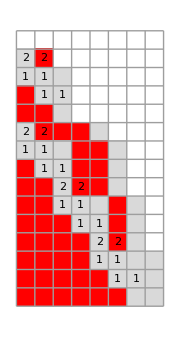
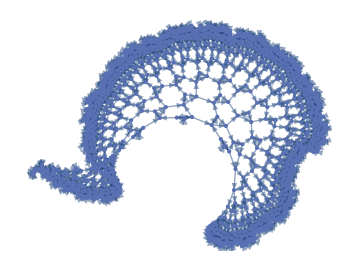
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1},{1,1,2},{1,6},{8,11},{1,1},{1,1,2},{1,13},{1,15},{1,1,2},{1,16},{1,18},{1,1,2},{1,19},{1,21},{23,26},{1,1},{1,1,2},{1,28},{1,30},{1,1,2},{1,31},{1,33},{1,1,2},{1,34},{1,36},{1,1,2},{1,37},{1,39},{1,1,2},{1,40},{1,42},{1,1,2},{1,43},{1,45},{1,1,2},{1,46},{1,48},{1,1,2},{1,49},{1,51},{53,56},{1,1},{1,1,2},{1,58},{1,60},{1,1,2},{1,61},{1,63},{1,1,2},{1,64},{1,66},{1,1,2},{1,67},{1,69},{1,1,2},{1,70},{1,72},{1,1,2},{1,73},{1,75},{1,1,2},{1,76},{1,78},{1,1,2},{1,79},{1,81},{1,1,2},{1,82},{1,84},{1,1,2},{1,85},{1,87},{1,1,2},{1,88},{1,90},{1,1,2},{1,91},{1,93},{1,1,2},{1,94},{1,96},{1,1,2},{1,97},{1,99},{1,1,2},{1,100},{1,102},{1,1,2},{1,103},{1,105},{1,1,2},{1,106},{1,108},{1,1,2},{1,109},{1,111},{113,116},{1,1},{1,1,2},{1,118},{1,120},{1,1,2},{1,121},{1,123},{1,1,2},{1,124},{1,126},{1,1,2},{1,127},{1,129},{1,1,2},{1,130},{1,132},{1,1,2},{1,133},{1,135},{1,1,2},{1,136},{1,138},{1,1,2},{1,139},{1,141},{1,1,2},{1,142},{1,144},{1,1,2},{1,145},{1,147},{1,1,2},{1,148},{1,150},{1,1,2},{1,151},{1,153},{1,1,2},{1,154},{1,156},{1,1,2},{1,157},{1,159},{1,1,2},{1,160},{1,162},{1,1,2},{1,163},{1,165},{1,1,2},{1,166},{1,168},{1,1,2},{1,169},{1,171},{1,1,2},{1,172},{1,174},{1,1,2},{1,175},{1,177},{1,1,2},{1,178},{1,180},{1,1,2},{1,181},{1,183},{1,1,2},{1,184},{1,186},{1,1,2},{1,187},{1,189},{1,1,2},{1,190},{1,192},{1,1,2},{1,193},{1,195},{1,1,2},{1,196},{1,198},{1,1,2},{1,199},{1,201},{1,1,2},{1,202},{1,204},{1,1,2},{1,205},{1,207},{1,1,2},{1,208},{1,210},{1,1,2},{1,211},{1,213},{1,1,2},{1,214},{1,216},{1,1,2},{1,217},{1,219},{1,1,2},{1,220},{1,222},{1,1,2},{1,223},{1,225},{1,1,2},{1,226},{1,228},{1,1,2},{1,229},{1,231},{233,236},{1,1},{1,1,2},{1,238},{1,240},{1,1,2},{1,241},{1,243},{1,1,2},{1,244},{1,246},{1,1,2},{1,247},{1,249},{1,1,2},{1,250},{1,252},{1,1,2},{1,253},{1,255},{1,1,2},{1,256},{1,258},{1,1,2},{1,259},{1,261},{1,1,2},{1,262},{1,264},{1,1,2},{1,265},{1,267},{1,1,2},{1,268},{1,270},{1,1,2},{1,271},{1,273},{1,1,2},{1,274},{1,276},{1,1,2},{1,277},{1,279},{1,1,2},{1,280},{1,282},{1,1,2},{1,283},{1,285},{1,1,2},{1,286},{1,288},{1,1,2},{1,289},{1,291},{1,1,2},{1,292},{1,294},{1,1,2},{1,295},{1,297},{1,1,2},{1,298},{1,300},{1,1,2},{1,301},{1,303},{1,1,2},{1,304},{1,306},{1,1,2},{1,307},{1,309},{1,1,2},{1,310},{1,312},{1,1,2},{1,313},{1,315},{1,1,2},{1,316},{1,318},{1,1,2},{1,319},{1,321},{1,1,2},{1,322},{1,324},{1,1,2},{1,325},{1,327},{1,1,2},{1,328},{1,330},{1,1,2},{1,331},{1,333},{1,1,2},{1,334},{1,336},{1,1,2},{1,337},{1,339},{1,1,2},{1,340},{1,342},{1,1,2},{1,343},{1,345},{1,1,2},{1,346},{1,348},{1,1,2},{1,349},{1,351},{1,1,2},{1,352},{1,354},{1,1,2},{1,355},{1,357},{1,1,2},{1,358},{1,360},{1,1,2},{1,361},{1,363},{1,1,2},{1,364},{1,366},{1,1,2},{1,367},{1,369},{1,1,2},{1,370},{1,372},{1,1,2},{1,373},{1,375},{1,1,2},{1,376},{1,378},{1,1,2},{1,379},{1,381},{1,1,2},{1,382},{1,384},{1,1,2},{1,385},{1,387},{1,1,2},{1,388},{1,390},{1,1,2},{1,391},{1,393},{1,1,2},{1,394},{1,396},{1,1,2},{1,397},{1,399},{1,1,2},{1,400},{1,402},{1,1,2},{1,403},{1,405},{1,1,2},{1,406},{1,408},{1,1,2},{1,409},{1,411},{1,1,2},{1,412},{1,414},{1,1,2},{1,415},{1,417},{1,1,2},{1,418},{1,420},{1,1,2},{1,421},{1,423},{1,1,2},{1,424},{1,426},{1,1,2},{1,427},{1,429},{1,1,2},{1,430},{1,432},{1,1,2},{1,433},{1,435},{1,1,2},{1,436},{1,438},{1,1,2},{1,439},{1,441},{1,1,2},{1,442},{1,444},{1,1,2},{1,445},{1,447},{1,1,2},{1,448},{1,450},{1,1,2},{1,451},{1,453},{1,1,2},{1,454},{1,456},{1,1,2},{1,457},{1,459},{1,1,2},{1,460},{1,462},{1,1,2},{1,463},{1,465},{1,1,2},{1,466},{1,468},{1,1,2},{1,469},{1,471},{473,476},{1,1},{1,1,2},{1,478},{1,480},{1,1,2},{1,481},{1,483},{1,1,2},{1,484},{1,486},{1,1,2},{1,487},{1,489},{1,1,2},{1,490},{1,492},{1,1,2},{1,493},{1,495},{1,1,2},{1,496},{1,498},{1,1,2},{1,499},{1,501},{1,1,2},{1,502},{1,504},{1,1,2},{1,505},{1,507},{1,1,2},{1,508},{1,510},{1,1,2},{1,511},{1,513},{1,1,2},{1,514},{1,516},{1,1,2},{1,517},{1,519},{1,1,2},{1,520},{1,522},{1,1,2},{1,523},{1,525},{1,1,2},{1,526},{1,528},{1,1,2},{1,529},{1,531},{1,1,2},{1,532},{1,534},{1,1,2},{1,535},{1,537},{1,1,2},{1,538},{1,540},{1,1,2},{1,541},{1,543},{1,1,2},{1,544},{1,546},{1,1,2},{1,547},{1,549},{1,1,2},{1,550},{1,552},{1,1,2},{1,553},{1,555},{1,1,2},{1,556},{1,558},{1,1,2},{1,559},{1,561},{1,1,2},{1,562},{1,564},{1,1,2},{1,565},{1,567},{1,1,2},{1,568},{1,570},{1,1,2},{1,571},{1,573},{1,1,2},{1,574},{1,576},{1,1,2},{1,577},{1,579},{1,1,2},{1,580},{1,582},{1,1,2},{1,583},{1,585},{1,1,2},{1,586},{1,588},{1,1,2},{1,589},{1,591},{1,1,2},{1,592},{1,594},{1,1,2},{1,595},{1,597},{1,1,2},{1,598},{1,600},{1,1,2},{1,601},{1,603},{1,1,2},{1,604},{1,606},{1,1,2},{1,607},{1,609},{1,1,2},{1,610},{1,612},{1,1,2},{1,613},{1,615},{1,1,2},{1,616},{1,618},{1,1,2},{1,619},{1,621},{1,1,2},{1,622},{1,624},{1,1,2},{1,625},{1,627},{1,1,2},{1,628},{1,630},{1,1,2},{1,631},{1,633},{1,1,2},{1,634},{1,636},{1,1,2},{1,637},{1,639},{1,1,2},{1,640},{1,642},{1,1,2},{1,643},{1,645},{1,1,2},{1,646},{1,648},{1,1,2},{1,649},{1,651},{1,1,2},{1,652},{1,654},{1,1,2},{1,655},{1,657},{1,1,2},{1,658},{1,660},{1,1,2},{1,661},{1,663},{1,1,2},{1,664},{1,666},{1,1,2},{1,667},{1,669},{1,1,2},{1,670},{1,672},{1,1,2},{1,673},{1,675},{1,1,2},{1,676},{1,678},{1,1,2},{1,679},{1,681},{1,1,2},{1,682},{1,684},{1,1,2},{1,685},{1,687},{1,1,2},{1,688},{1,690},{1,1,2},{1,691},{1,693},{1,1,2},{1,694},{1,696},{1,1,2},{1,697},{1,699},{1,1,2},{1,700},{1,702},{1,1,2},{1,703},{1,705},{1,1,2},{1,706},{1,708},{1,1,2},{1,709},{1,711},{1,1,2},{1,712},{1,714},{1,1,2},{1,715},{1,717},{1,1,2},{1,718},{1,720},{1,1,2},{1,721},{1,723},{1,1,2},{1,724},{1,726},{1,1,2},{1,727},{1,729},{1,1,2},{1,730},{1,732},{1,1,2},{1,733},{1,735},{1,1,2},{1,736},{1,738},{1,1,2},{1,739},{1,741},{1,1,2},{1,742},{1,744},{1,1,2},{1,745},{1,747},{1,1,2},{1,748},{1,750},{1,1,2},{1,751},{1,753},{1,1,2},{1,754},{1,756},{1,1,2},{1,757},{1,759},{1,1,2},{1,760},{1,762},{1,1,2},{1,763},{1},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{},{1,1},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}},{1,1,2},2·{{1}}}

{3,2,1,1,3,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,3,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2,1,1,2}

{{exp,{1,1,4,2},5
11
15,1 | 5 | 16 | 42 | 98 | 214 | 450 | 926
4 | 11 | 26 | 56 | 116 | 236 | 476 | 
7 | 15 | 30 | 60 | 120 | 240 |  | },{exp,{1,1,3,2},13
26
30,3 | 13 | 39 | 95 | 211 | 447 | 923
10 | 26 | 56 | 116 | 236 | 476 | 
16 | 30 | 60 | 120 | 240 |  | },{failed,1 | 2 | 4 | 7 | 14 | 26 | 46 | 72 | 116
1 | 2 | 3 | 7 | 12 | 20 | 26 | 44 | 
1 | 1 | 4 | 5 | 8 | 6 | 18 |  | 
0 | 3 | 1 | 3 | -2 | 12 |  |  | 
3 | -2 | 2 | -5 | 14 |  |  |  | 
-5 | 4 | -7 | 19 |  |  |  |  | },{exp,{1,0,4,2},4
11
15,4 | 15 | 41 | 97 | 213 | 449 | 925
11 | 26 | 56 | 116 | 236 | 476 | 
15 | 30 | 60 | 120 | 240 |  | }}

```mathematica
ssst0=SSS[{"AA"->"BA","AB"->"AAA",""->"AB"},"",1500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 1269438023, "QCode" -> "3433322342431", "RuleSet" -> {"ABAAA" -> "A", "AB" -> "BA", "" -> "A"}], " : ", {"failed", "failed", "3D", "failed"}, " - ", "OK"]

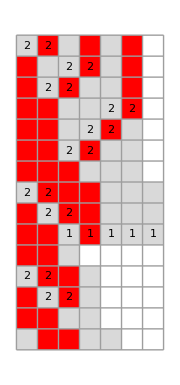
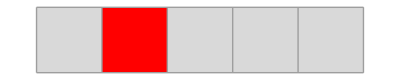
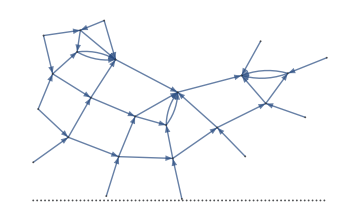
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{2,7},{1,3},{3,6},{1,6},{1,5},{4,4},{1},{1,4},{1,4},{9},{1},{1,3},{3,6},{1},{1,3},{3,3},{1},{1,3},{6},{1},{2,4},{1},{2,2},{1}}

{{2,7},{1,3},{3,6},{1,6},{1,5},{4,4},{1},2·{{1,4}},{9},{1},{1,3},{3,6},{1},{1,3},{3,3},{1},{1,3},{6},{1},{2,4},{1},{2,2},{1}}

{2,2,2,2,2,2,3,2,2,1,3,2,2,3,2,2,3,2,1,3,2,3,2,3,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

Part::partw: Part 26 of {0,1,2,3,4,2,2,1,2,3,«15»} does not exist.

Part::take: Cannot take positions 25 through 23 in {2,2,2,2,2,2,3,2,2,1,«90»}.

Part::take: Cannot take positions 24 through 21 in {2,2,2,2,2,2,3,2,2,1,«90»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

```mathematica
ssst0=SSS[{"ABAAA"->"A","AB"->"BA",""->"A"},"ABABAB",100,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 5812190580, "QCode" -> "32234243433143", "RuleSet" -> {"AA" -> "A", "AB" -> "BBAA", "" -> "BA"}], " : ", {"exp1", "exp1", "exp2", "exp1"}, " - ", "OK"]

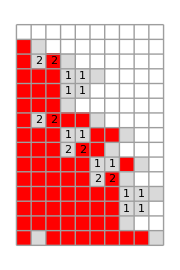
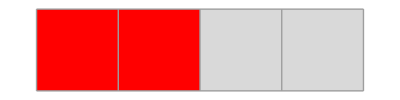
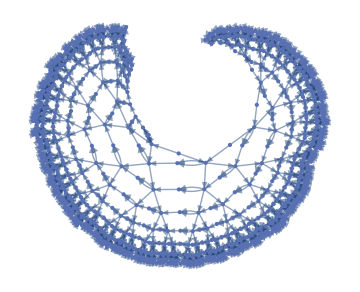
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{2,4},{1,5},{1,1,6,8},{1},{8},{1,9},{1,1,10,12},{1},{1,1,12,14},{1},{1,1,14,16},{1},{16},{1,17},{1,1,18,20},{1},{1,1,20,22},{1},{1,1,22,24},{1},{1,1,24,26},{1},{1,1,26,28},{1},{1,1,28,30},{1},{1,1,30,32},{1},{32},{1,33},{1,1,34,36},{1},{1,1,36,38},{1},{1,1,38,40},{1},{1,1,40,42},{1},{1,1,42,44},{1},{1,1,44,46},{1},{1,1,46,48},{1},{1,1,48,50},{1},{1,1,50,52},{1},{1,1,52,54},{1},{1,1,54,56},{1},{1,1,56,58},{1},{1,1,58,60},{1},{1,1,60,62},{1},{1,1,62,64},{1},{64},{1,65},{1,1,66,68},{1},{1,1,68,70},{1},{1,1,70,72},{1},{1,1,72,74},{1},{1,1,74,76},{1},{1,1,76,78},{1},{1,1,78,80},{1},{1,1,80,82},{1},{1,1,82,84},{1},{1,1,84,86},{1},{1,1,86,88},{1},{1,1,88,90},{1},{1,1,90,92},{1},{1,1,92,94},{1},{1,1,94,96},{1},{1,1,96,98},{1},{1,1,98,100},{1},{1,1,100,102},{1},{1,1,102,104},{1},{1,1,104,106},{1},{1,1,106,108},{1},{1,1,108,110},{1},{1,1,110,112},{1},{1,1,112,114},{1},{1,1,114,116},{1},{1,1,116,118},{1},{1,1,118,120},{1},{1,1,120,122},{1},{1,1,122,124},{1},{1,1,124,126},{1},{1,1,126,128},{1},{128},{1,129},{1,1,130,132},{1},{1,1,132,134},{1},{1,1,134,136},{1},{1,1,136,138},{1},{1,1,138,140},{1},{1,1,140,142},{1},{1,1,142,144},{1},{1,1,144,146},{1},{1,1,146,148},{1},{1,1,148,150},{1},{1,1,150,152},{1},{1,1,152,154},{1},{1,1,154,156},{1},{1,1,156,158},{1},{1,1,158,160},{1},{1,1,160,162},{1},{1,1,162,164},{1},{1,1,164,166},{1},{1,1,166,168},{1},{1,1,168,170},{1},{1,1,170,172},{1},{1,1,172,174},{1},{1,1,174,176},{1},{1,1,176,178},{1},{1,1,178,180},{1},{1,1,180,182},{1},{1,1,182,184},{1},{1,1,184,186},{1},{1,1,186,188},{1},{1,1,188,190},{1},{1,1,190,192},{1},{1,1,192,194},{1},{1,1,194,196},{1},{1,1,196,198},{1},{1,1,198,200},{1},{1,1,200,202},{1},{1,1,202,204},{1},{1,1,204,206},{1},{1,1,206,208},{1},{1,1,208,210},{1},{1,1,210,212},{1},{1,1,212,214},{1},{1,1,214,216},{1},{1,1,216,218},{1},{1,1,218,220},{1},{1,1,220,222},{1},{1,1,222,224},{1},{1,1,224,226},{1},{1,1,226,228},{1},{1,1,228,230},{1},{1,1,230,232},{1},{1,1,232,234},{1},{1,1,234,236},{1},{1,1,236,238},{1},{1,1,238,240},{1},{1,1,240,242},{1},{1,1,242,244},{1},{1,1,244,246},{1},{1,1,246,248},{1},{1,1,248,250},{1},{1,1,250,252},{1},{1,1,252,254},{1},{1,1,254,256},{1},{256},{1,257},{1,1,258,260},{1},{1,1,260,262},{1},{1,1,262,264},{1},{1,1,264,266},{1},{1,1,266,268},{1},{1,1,268,270},{1},{1,1,270,272},{1},{1,1,272,274},{1},{1,1,274,276},{1},{1,1,276,278},{1},{1,1,278,280},{1},{1,1,280,282},{1},{1,1,282,284},{1},{1,1,284,286},{1},{1,1,286,288},{1},{1,1,288,290},{1},{1,1,290,292},{1},{1,1,292,294},{1},{1,1,294,296},{1},{1,1,296,298},{1},{1,1,298,300},{1},{1,1,300,302},{1},{1,1,302,304},{1},{1,1,304,306},{1},{1,1,306,308},{1},{1,1,308,310},{1},{1,1,310,312},{1},{1,1,312,314},{1},{1,1,314,316},{1},{1,1,316,318},{1},{1,1,318,320},{1},{1,1,320,322},{1},{1,1,322,324},{1},{1,1,324,326},{1},{1,1,326,328},{1},{1,1,328,330},{1},{1,1,330,332},{1},{1,1,332,334},{1},{1,1,334,336},{1},{1,1,336,338},{1},{1,1,338,340},{1},{1,1,340,342},{1},{1,1,342,344},{1},{1,1,344,346},{1},{1,1,346,348},{1},{1,1,348,350},{1},{1,1,350,352},{1},{1,1,352,354},{1},{1,1,354,356},{1},{1,1,356,358},{1},{1,1,358,360},{1},{1,1,360,362},{1},{1,1,362,364},{1},{1,1,364,366},{1},{1,1,366,368},{1},{1,1,368,370},{1},{1,1,370,372},{1},{1,1,372,374},{1},{1,1,374,376},{1},{1,1,376,378},{1},{1,1,378,380},{1},{1,1,380,382},{1},{1,1,382,384},{1},{1,1,384,386},{1},{1,1,386,388},{1},{1,1,388,390},{1},{1,1,390,392},{1},{1,1,392,394},{1},{1,1,394,396},{1},{1,1,396,398},{1},{1,1,398,400},{1},{1,1,400,402},{1},{1,1,402,404},{1},{1,1,404,406},{1},{1,1,406,408},{1},{1,1,408,410},{1},{1,1,410,412},{1},{1,1,412,414},{1},{1,1,414,416},{1},{1,1,416,418},{1},{1,1,418,420},{1},{1,1,420,422},{1},{1,1,422,424},{1},{1,1,424,426},{1},{1,1,426,428},{1},{1,1,428,430},{1},{1,1,430,432},{1},{1,1,432,434},{1},{1,1,434,436},{1},{1,1,436,438},{1},{1,1,438,440},{1},{1,1,440,442},{1},{1,1,442,444},{1},{1,1,444,446},{1},{1,1,446,448},{1},{1,1,448,450},{1},{1,1,450,452},{1},{1,1,452,454},{1},{1,1,454,456},{1},{1,1,456,458},{1},{1,1,458,460},{1},{1,1,460,462},{1},{1,1,462,464},{1},{1,1,464,466},{1},{1,1,466,468},{1},{1,1,468,470},{1},{1,1,470,472},{1},{1,1,472,474},{1},{1,1,474,476},{1},{1,1,476,478},{1},{1,1,478,480},{1},{1,1,480,482},{1},{1,1,482,484},{1},{1,1,484,486},{1},{1,1,486,488},{1},{1,1,488,490},{1},{1,1,490,492},{1},{1,1,492,494},{1},{1,1,494,496},{1},{1,1,496,498},{1},{1,1,498,500},{1},{1,1,500,502},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
ssst0=SSS[{"AA"->"A","AB"->"BBAA",""->"BA"},"",1000,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6007493776, "QCode" -> "33134243133434", "RuleSet" -> {"AAA" -> "", "AB" -> "BA", "" -> "AABB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

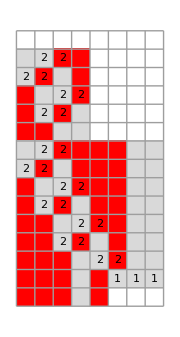
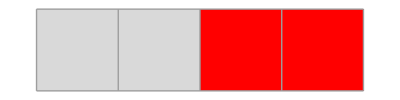
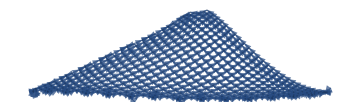
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2,3},{1,2},{2,8},{1,10},{8,9},{1,1,2,3},{1,2},{2,13},{1,2},{2,13},{1,2},{3,13},{1,2},{},{12,14},{1,1,2,3},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{1,17},{},{1,1,2,3},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,22},{20,21},{1,1,2,3},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{3,25},{1,2},{},{24,26},{1,1,2,3},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{1,29},{},{1,1,2,3},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,34},{32,33},{1,1,2,3},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{3,37},{1,2},{},{36,38},{1,1,2,3},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{1,41},{},{1,1,2,3},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,46},{44,45},{1,1,2,3},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{2,49},{1,2},{3,49},{1,2},{},{48,50},{1,1,2,3},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{1,53},{},{1,1,2,3},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,58},{56,57},{1,1,2,3},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{2,61},{1,2},{3},{1,2},{},{},{1,1,2,3},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1}}

```mathematica
ssst0=SSS[{"AAA"->"","AB"->"BA",""->"AABB"},"",500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6007493876, "QCode" -> "33134243134334", "RuleSet" -> {"AAA" -> "", "AB" -> "BA", "" -> "ABAB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

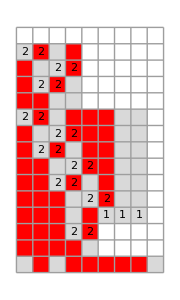
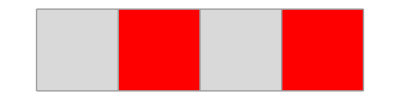
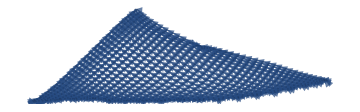
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2,2},{2,7},{1,9},{7,8},{1,1,2,2},{2,12},{1,2},{2,12},{1,2},{3,12},{1,2},{},{11,13},{1,1,2,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{1,16},{},{1,1,2,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,21},{19,20},{1,1,2,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{3,24},{1,2},{},{23,25},{1,1,2,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{2,28},{1,2},{1,28},{},{1,1,2,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,33},{31,32},{1,1,2,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{3,36},{1,2},{},{35,37},{1,1,2,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{1,40},{},{1,1,2,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,45},{43,44},{1,1,2,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{2,48},{1,2},{3,48},{1,2},{},{47,49},{1,1,2,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{2,52},{1,2},{1,52},{},{1,1,2,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,2},{2,55},{1,57},{55,56},{1,1,2,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{3,60},{1,2},{},{59,61},{1,1,2,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{2,64},{1,2},{1,64},{},{1,1,2,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,2},{2,67},{1,69},{67,68},{1,1,2,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{2,72},{1,2},{3,72},{1,2},{},{71,73},{1,1,2,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2,76},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{1},{},{1,1,2,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1}}

```mathematica
ssst0=SSS[{"AAA"->"","AB"->"BA",""->"ABAB"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6007493880, "QCode" -> "33134243134343", "RuleSet" -> {"AAA" -> "", "AB" -> "BA", "" -> "ABBA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

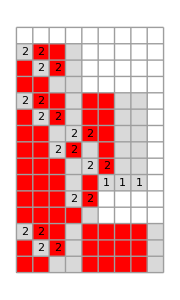
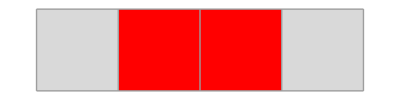
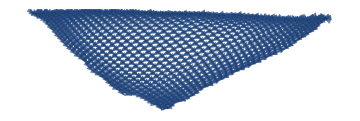
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2,9},{1,5},{6,7},{1,1,2,3},{1,10},{2,11},{1,2},{3,11},{1,2},{},{10,12},{1,1,2,3},{1,14},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{1,15},{},{1,1,2,3},{1,17},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,20},{18,19},{1,1,2,3},{1,22},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{3,23},{1,2},{},{22,24},{1,1,2,3},{1,26},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{1,27},{},{1,1,2,3},{1,29},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,32},{30,31},{1,1,2,3},{1,34},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{3,35},{1,2},{},{34,36},{1,1,2,3},{1,38},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{1,39},{},{1,1,2,3},{1,41},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,44},{42,43},{1,1,2,3},{1,46},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{3,47},{1,2},{},{46,48},{1,1,2,3},{1,50},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{1,51},{},{1,1,2,3},{1,53},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,56},{54,55},{1,1,2,3},{1,58},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{3,59},{1,2},{},{58,60},{1,1,2,3},{1,62},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{1,63},{},{1,1,2,3},{1,65},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,68},{66,67},{1,1,2,3},{1,70},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{2,71},{1,2},{3,71},{1,2},{},{70,72},{1,1,2,3},{1,74},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{2,75},{1,2},{1,75},{},{1,1,2,3},{1,77},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,2},{2,78},{1,80},{78,79},{1,1,2,3},{1,82},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2,83},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{3},{1,2},{},{},{1,1,2,3},{1},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1}}

$Aborted

{3,2,2,3,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

Part::take: Cannot take positions 832 through 830 in {3,2,2,3,2,2,2,2,2,1,«890»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

```mathematica
ssst0=SSS[{"AAA"->"","AB"->"BA",""->"ABBA"},"",900,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6007494376, "QCode" -> "33134243143334", "RuleSet" -> {"AAA" -> "", "AB" -> "BA", "" -> "BAAB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

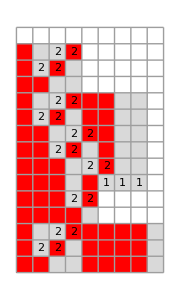
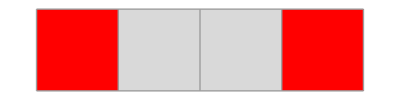
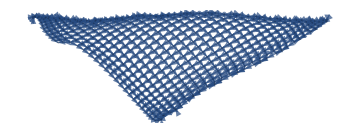
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2,6},{1,8},{6,7},{1,1,2,11},{1,2},{2,11},{1,2},{3,11},{1,2},{},{10,12},{1,1,2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{1,15},{},{1,1,2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,2},{2,18},{1,20},{18,19},{1,1,2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{3,23},{1,2},{},{22,24},{1,1,2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{1,27},{},{1,1,2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,32},{30,31},{1,1,2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{3,35},{1,2},{},{34,36},{1,1,2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{1,39},{},{1,1,2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,2},{2,42},{1,44},{42,43},{1,1,2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{3,47},{1,2},{},{46,48},{1,1,2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{1,51},{},{1,1,2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,2},{2,54},{1,56},{54,55},{1,1,2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{2,59},{1,2},{3,59},{1,2},{},{58,60},{1,1,2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{1},{},{1,1,2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1}}

$Aborted

{3,2,2,3,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

Part::take: Cannot take positions 414 through 412 in {3,2,2,3,2,2,2,2,2,1,«490»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

```mathematica
ssst0=SSS[{"AAA"->"","AB"->"BA",""->"BAAB"},"",500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6144515075, "QCode" -> "33424332324133", "RuleSet" -> {"AAB" -> "BAA", "AA" -> "B", "" -> "AAA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

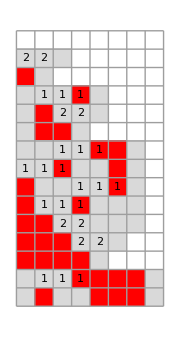


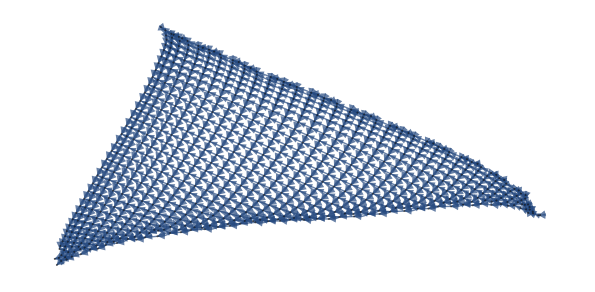
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1},{2},{1,1,4},{1,1,3},{4},2·{{1,2,2}},{2,2,6},{1,3,3},{1,1,5},2·{{5}},{1,1,7},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{10},2·{{1,2,2}},{2,2,12},{1,2,2},{2,2,11},{1,2,2},{2,2,10},{1,2,2},{2,2,9},{1,3,3},{1,1,8},2·{{8}},{1,1,10},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{16},2·{{1,2,2}},{2,2,18},{1,2,2},{2,2,17},{1,2,2},{2,2,16},{1,2,2},{2,2,15},{1,2,2},{2,2,14},{1,2,2},{2,2,13},{1,2,2},{2,2,12},{1,3,3},{1,1,11},2·{{11}},{1,1,13},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{1,1,17},{1,1,18},{1,1,19},{1,1,20},{1,1,21},{22},2·{{1,2,2}},{2,2,24},{1,2,2},{2,2,23},{1,2,2},{2,2,22},{1,2,2},{2,2,21},{1,2,2},{2,2,20},{1,2,2},{2,2,19},{1,2,2},{2,2,18},{1,2,2},{2,2,17},{1,2,2},{2,2,16},{1,2,2},{2,2,15},{1,3,3},{1,1,14},2·{{14}},{1,1,16},{1,1,15},{1,1,16},{1,1,17},{1,1,18},{1,1,19},{1,1,20},{1,1,21},{1,1,22},{1,1,23},{1,1,24},{1,1,25},{1,1,26},{1,1,27},{28},2·{{1,2,2}},{2,2,30},{1,2,2},{2,2,29},{1,2,2},{2,2,28},{1,2,2},{2,2,27},{1,2,2},{2,2,26},{1,2,2},{2,2,25},{1,2,2},{2,2,24},{1,2,2},{2,2,23},{1,2,2},{2,2,22},{1,2,2},{2,2,21},{1,2,2},{2,2,20},{1,2,2},{2,2,19},{1,2,2},{2,2,18},{1,3,3},{1,1,17},2·{{17}},{1,1,19},{1,1,18},{1,1,19},{1,1,20},{1,1,21},{1,1,22},{1,1,23},{1,1,24},{1,1,25},{1,1,26},{1,1,27},{1,1,28},{1,1,29},{1,1,30},{1,1,31},{1,1,32},{1,1,33},{34},2·{{1,2,2}},{2,2,36},{1,2,2},{2,2,35},{1,2,2},{2,2,34},{1,2,2},{2,2,33},{1,2,2},{2,2,32},{1,2,2},{2,2,31},{1,2,2},{2,2,30},{1,2,2},{2,2,29},{1,2,2},{2,2,28},{1,2,2},{2,2,27},{1,2,2},{2,2,26},{1,2,2},{2,2,25},{1,2,2},{2,2,24},{1,2,2},{2,2,23},{1,2,2},{2,2,22},{1,2,2},{2,2,21},{1,3,3},{1,1,20},2·{{20}},{1,1,22},{1,1,21},{1,1,22},{1,1,23},{1,1,24},{1,1,25},{1,1,26},{1,1,27},{1,1,28},{1,1,29},{1,1,30},{1,1,31},{1,1,32},{1,1,33},{1,1,34},{1,1,35},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{40},2·{{1,2,2}},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2,39},{1,2,2},{2,2,38},{1,2,2},{2,2,37},{1,2,2},{2,2,36},{1,2,2},{2,2,35},{1,2,2},{2,2,34},{1,2,2},{2,2,33},{1,2,2},{2,2,32},{1,2,2},{2,2,31},{1,2,2},{2,2,30},{1,2,2},{2,2,29},{1,2,2},{2,2,28},{1,2,2},{2,2,27},{1,2,2},{2,2,26},{1,2,2},{2,2,25},{1,2,2},{2,2,24},{1,3,3},{1,1,23},2·{{23}},{1,1,25},{1,1,24},{1,1,25},{1,1,26},{1,1,27},{1,1,28},{1,1,29},{1,1,30},{1,1,31},{1,1,32},{1,1,33},{1,1,34},{1,1,35},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{1,1,40},{1,1,41},{1,1,42},{1,1,43},{1,1,44},{1,1,45},{46},2·{{1,2,2}},{2,2,48},{1,2,2},{2,2,47},{1,2,2},{2,2,46},{1,2,2},{2,2,45},{1,2,2},{2,2,44},{1,2,2},{2,2,43},{1,2,2},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2,39},{1,2,2},{2,2,38},{1,2,2},{2,2,37},{1,2,2},{2,2,36},{1,2,2},{2,2,35},{1,2,2},{2,2,34},{1,2,2},{2,2,33},{1,2,2},{2,2,32},{1,2,2},{2,2,31},{1,2,2},{2,2,30},{1,2,2},{2,2,29},{1,2,2},{2,2,28},{1,2,2},{2,2,27},{1,3,3},{1,1,26},2·{{26}},{1,1,28},{1,1,27},{1,1,28},{1,1,29},{1,1,30},{1,1,31},{1,1,32},{1,1,33},{1,1,34},{1,1,35},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{1,1,40},{1,1,41},{1,1,42},{1,1,43},{1,1,44},{1,1,45},{1,1,46},{1,1,47},{1,1,48},{1,1,49},{1,1,50},{1,1,51},{52},2·{{1,2,2}},{2,2,54},{1,2,2},{2,2,53},{1,2,2},{2,2,52},{1,2,2},{2,2,51},{1,2,2},{2,2,50},{1,2,2},{2,2,49},{1,2,2},{2,2,48},{1,2,2},{2,2,47},{1,2,2},{2,2,46},{1,2,2},{2,2,45},{1,2,2},{2,2,44},{1,2,2},{2,2,43},{1,2,2},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2,39},{1,2,2},{2,2,38},{1,2,2},{2,2,37},{1,2,2},{2,2,36},{1,2,2},{2,2,35},{1,2,2},{2,2,34},{1,2,2},{2,2,33},{1,2,2},{2,2,32},{1,2,2},{2,2,31},{1,2,2},{2,2,30},{1,3,3},{1,1,29},2·{{29}},{1,1,31},{1,1,30},{1,1,31},{1,1,32},{1,1,33},{1,1,34},{1,1,35},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{1,1,40},{1,1,41},{1,1,42},{1,1,43},{1,1,44},{1,1,45},{1,1,46},{1,1,47},{1,1,48},{1,1,49},{1,1,50},{1,1,51},{1,1,52},{1,1,53},{1,1,54},{1,1,55},{1,1,56},{1,1,57},{58},2·{{1,2,2}},{2,2,60},{1,2,2},{2,2,59},{1,2,2},{2,2,58},{1,2,2},{2,2,57},{1,2,2},{2,2,56},{1,2,2},{2,2,55},{1,2,2},{2,2,54},{1,2,2},{2,2,53},{1,2,2},{2,2,52},{1,2,2},{2,2,51},{1,2,2},{2,2,50},{1,2,2},{2,2,49},{1,2,2},{2,2,48},{1,2,2},{2,2,47},{1,2,2},{2,2,46},{1,2,2},{2,2,45},{1,2,2},{2,2,44},{1,2,2},{2,2,43},{1,2,2},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2,39},{1,2,2},{2,2,38},{1,2,2},{2,2,37},{1,2,2},{2,2,36},{1,2,2},{2,2,35},{1,2,2},{2,2,34},{1,2,2},{2,2,33},{1,3,3},{1,1,32},2·{{32}},{1,1,34},{1,1,33},{1,1,34},{1,1,35},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{1,1,40},{1,1,41},{1,1,42},{1,1,43},{1,1,44},{1,1,45},{1,1,46},{1,1,47},{1,1,48},{1,1,49},{1,1,50},{1,1,51},{1,1,52},{1,1,53},{1,1,54},{1,1,55},{1,1,56},{1,1,57},{1,1,58},{1,1,59},{1,1,60},{1,1,61},{1,1,62},{1,1,63},{64},2·{{1,2,2}},{2,2,66},{1,2,2},{2,2,65},{1,2,2},{2,2,64},{1,2,2},{2,2,63},{1,2,2},{2,2,62},{1,2,2},{2,2,61},{1,2,2},{2,2,60},{1,2,2},{2,2,59},{1,2,2},{2,2,58},{1,2,2},{2,2,57},{1,2,2},{2,2,56},{1,2,2},{2,2,55},{1,2,2},{2,2,54},{1,2,2},{2,2,53},{1,2,2},{2,2,52},{1,2,2},{2,2,51},{1,2,2},{2,2,50},{1,2,2},{2,2,49},{1,2,2},{2,2,48},{1,2,2},{2,2,47},{1,2,2},{2,2,46},{1,2,2},{2,2,45},{1,2,2},{2,2,44},{1,2,2},{2,2,43},{1,2,2},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2,39},{1,2,2},{2,2,38},{1,2,2},{2,2,37},{1,2,2},{2,2,36},{1,3,3},{1,1,35},2·{{35}},{1,1,37},{1,1,36},{1,1,37},{1,1,38},{1,1,39},{1,1,40},{1,1,41},{1,1,42},{1,1,43},{1,1,44},{1,1,45},{1,1,46},{1,1,47},{1,1,48},{1,1,49},{1,1,50},{1,1,51},{1,1,52},{1,1,53},{1,1,54},{1,1,55},{1,1,56},{1,1,57},{1,1,58},{1,1,59},{1,1,60},{1,1,61},{1,1,62},{1,1,63},{1,1,64},{1,1,65},{1,1,66},{1,1,67},{1,1,68},{1,1,69},{70},2·{{1,2,2}},{2,2,72},{1,2,2},{2,2,71},{1,2,2},{2,2,70},{1,2,2},{2,2,69},{1,2,2},{2,2,68},{1,2,2},{2,2,67},{1,2,2},{2,2,66},{1,2,2},{2,2,65},{1,2,2},{2,2,64},{1,2,2},{2,2,63},{1,2,2},{2,2,62},{1,2,2},{2,2,61},{1,2,2},{2,2,60},{1,2,2},{2,2,59},{1,2,2},{2,2,58},{1,2,2},{2,2,57},{1,2,2},{2,2,56},{1,2,2},{2,2,55},{1,2,2},{2,2,54},{1,2,2},{2,2,53},{1,2,2},{2,2,52},{1,2,2},{2,2,51},{1,2,2},{2,2,50},{1,2,2},{2,2,49},{1,2,2},{2,2,48},{1,2,2},{2,2,47},{1,2,2},{2,2,46},{1,2,2},{2,2,45},{1,2,2},{2,2,44},{1,2,2},{2,2,43},{1,2,2},{2,2,42},{1,2,2},{2,2,41},{1,2,2},{2,2,40},{1,2,2},{2,2},{1,3,3},{1,1},2·{{}},33·{{1,1}}}

```mathematica
ssst0=SSS[{"AAB"->"BAA","AA"->"B",""->"AAA"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

```mathematica
{{"failed",},{"failed"},{"2D",{12,0,26,3/4},{{1, 2, 3, 6, 9, 12, 17, 23, 28, 35, 43, 51}, {1, 1, 3, 3, 3, 5, 6, 5, 7, 8, 8, 9}, {0, 2, 0, 0, 2, 1, -1, 2, 1, 0, 1, 1}},{{1, 2, 3, 6, 9, 12, 17, 23, 28, 35, 43, 51, 60, 70, 80, 92, 104, 116, 130, 145, 159, 175, 192, 209, 227, 246, 265, 286, 307, 328, 351, 375, 398, 423, 449, 475, 502, 530, 558}, {1, 1, 3, 3, 3, 5, 6, 5, 7, 8, 8, 9, 10, 10, 12, 12, 12, 14, 15, 14, 16, 17, 17, 18, 19, 19, 21, 21, 21, 23, 24, 23, 25, 26, 26, 27, 28, 28, }, {0, 2, 0, 0, 2, 1, -1, 2, 1, 0, 1, 1, 0, 2, 0, 0, 2, 1, -1, 2, 1, 0, 1, 1, 0, 2, 0, 0, 2, 1, -1, 2, 1, 0, 1, 1, 0, , }}},{"failed"}}
```

```mathematica
CheckDimension[{9,19,48,68,117,147,216,256,345,395,504,564,693,763,912}]
```

{failed,9 | 19 | 48 | 68 | 117 | 147 | 216 | 256 | 345 | 395 | 504 | 564 | 693 | 763 | 912
10 | 29 | 20 | 49 | 30 | 69 | 40 | 89 | 50 | 109 | 60 | 129 | 70 | 149 | 
19 | -9 | 29 | -19 | 39 | -29 | 49 | -39 | 59 | -49 | 69 | -59 | 79 |  | 
-28 | 38 | -48 | 58 | -68 | 78 | -88 | 98 | -108 | 118 | -128 | 138 |  |  | 
66 | -86 | 106 | -126 | 146 | -166 | 186 | -206 | 226 | -246 | 266 |  |  |  | 
-152 | 192 | -232 | 272 | -312 | 352 | -392 | 432 | -472 | 512 |  |  |  |  | 
344 | -424 | 504 | -584 | 664 | -744 | 824 | -904 | 984 |  |  |  |  |  | 
-768 | 928 | -1088 | 1248 | -1408 | 1568 | -1728 | 1888 |  |  |  |  |  |  | 
1696 | -2016 | 2336 | -2656 | 2976 | -3296 | 3616 |  |  |  |  |  |  |  | 
-3712 | 4352 | -4992 | 5632 | -6272 | 6912 |  |  |  |  |  |  |  |  | 
8064 | -9344 | 10624 | -11904 | 13184 |  |  |  |  |  |  |  |  |  | 
-17408 | 19968 | -22528 | 25088 |  |  |  |  |  |  |  |  |  |  | }

#### SequenceForm[Association["Index" -> 6308200376, "QCode" -> "34243233241334", "RuleSet" -> {"AB" -> "BA", "AAA" -> "B", "" -> "AAB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

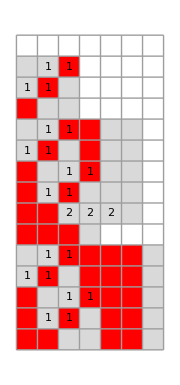
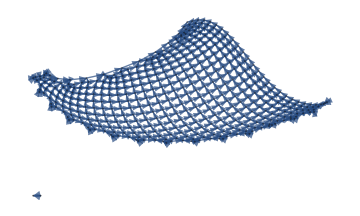
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{failed,9 | 19 | 48 | 68 | 117 | 147 | 216 | 256 | 345 | 395
10 | 29 | 20 | 49 | 30 | 69 | 40 | 89 | 50 | 
19 | -9 | 29 | -19 | 39 | -29 | 49 | -39 |  | 
-28 | 38 | -48 | 58 | -68 | 78 | -88 |  |  | 
66 | -86 | 106 | -126 | 146 | -166 |  |  |  | 
-152 | 192 | -232 | 272 | -312 |  |  |  |  | 
344 | -424 | 504 | -584 |  |  |  |  |  | },{failed,5 | 11 | 34 | 50 | 93 | 119 | 182 | 218 | 301 | 347
6 | 23 | 16 | 43 | 26 | 63 | 36 | 83 | 46 | 
17 | -7 | 27 | -17 | 37 | -27 | 47 | -37 |  | 
-24 | 34 | -44 | 54 | -64 | 74 | -84 |  |  | 
58 | -78 | 98 | -118 | 138 | -158 |  |  |  | 
-136 | 176 | -216 | 256 | -296 |  |  |  |  | 
312 | -392 | 472 | -552 |  |  |  |  |  | },{failed,1 | 3 | 6 | 11 | 18 | 27 | 38 | 52 | 67 | 86 | 105 | 128
2 | 3 | 5 | 7 | 9 | 11 | 14 | 15 | 19 | 19 | 23 | 
1 | 2 | 2 | 2 | 2 | 3 | 1 | 4 | 0 | 4 |  | 
1 | 0 | 0 | 0 | 1 | -2 | 3 | -4 | 4 |  |  | 
-1 | 0 | 0 | 1 | -3 | 5 | -7 | 8 |  |  |  | 
1 | 0 | 1 | -4 | 8 | -12 | 15 |  |  |  |  | 
-1 | 1 | -5 | 12 | -20 | 27 |  |  |  |  |  | 
2 | -6 | 17 | -32 | 47 |  |  |  |  |  |  | 
-8 | 23 | -49 | 79 |  |  |  |  |  |  |  | },{failed,3 | 19 | 31 | 68 | 90 | 147 | 179 | 256 | 298 | 395 | 447
16 | 12 | 37 | 22 | 57 | 32 | 77 | 42 | 97 | 52 | 
-4 | 25 | -15 | 35 | -25 | 45 | -35 | 55 | -45 |  | 
29 | -40 | 50 | -60 | 70 | -80 | 90 | -100 |  |  | 
-69 | 90 | -110 | 130 | -150 | 170 | -190 |  |  |  | 
159 | -200 | 240 | -280 | 320 | -360 |  |  |  |  | 
-359 | 440 | -520 | 600 | -680 |  |  |  |  |  | 
799 | -960 | 1120 | -1280 |  |  |  |  |  |  | }}

{{1,1,2},{1,17},{4,6},{1,1,2},{1,2},{2,7},{1,2},{1,7},{8},{1,1,2},{1,2},{2,11},{1,2},{2,11},{1,2},{2,11},{1,2},{1,11},{12},{1,1,2},{1,2},{2,14},{1,2},{2,14},{1,2},{2,14},{1,2},{2,14},{1,2},{2,14},{1,37},{14,16},{1,1,2},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{1,17},{18},{1,1,2},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{1,21},{22},{1,1,2},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,57},{24,26},{1,1,2},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{2,27},{1,2},{1,27},{28},{1,1,2},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{2,31},{1,2},{1,31},{32},{1,1,2},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,2},{2,34},{1,77},{34,36},{1,1,2},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{2,37},{1,2},{1,37},{38},{1,1,2},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{2,41},{1,2},{1,41},{42},{1,1,2},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,2},{2,44},{1,97},{44,46},{1,1,2},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{2,47},{1,2},{1,47},{48},{1,1,2},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{2,51},{1,2},{1,51},{52},{1,1,2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1},{},{1,1}}

```mathematica
ssst0=SSS[{"AB"->"BA","AAA"->"B",""->"AAB"},"",650,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

#### SequenceForm[Association["Index" -> 6308200380, "QCode" -> "34243233241343", "RuleSet" -> {"AB" -> "BA", "AAA" -> "B", "" -> "ABA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

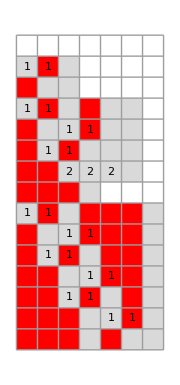

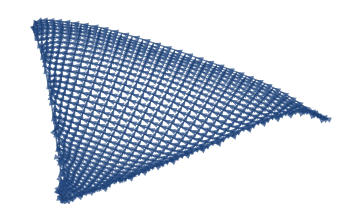
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,15},{3,5},{1,1,2},{2,6},{1,2},{1,6},{7},{1,1,2},{2,10},{1,2},{2,10},{1,2},{2,10},{1,2},{1,10},{11},{1,1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,35},{13,15},{1,1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{1,16},{17},{1,1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{2,20},{1,2},{1,20},{21},{1,1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,2},{2,23},{1,55},{23,25},{1,1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{2,26},{1,2},{1,26},{27},{1,1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{2,30},{1,2},{1,30},{31},{1,1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,2},{2,33},{1,75},{33,35},{1,1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{2,36},{1,2},{1,36},{37},{1,1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{2,40},{1,2},{1,40},{41},{1,1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,2},{2,43},{1,95},{43,45},{1,1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{2,46},{1,2},{1,46},{47},{1,1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{2,50},{1,2},{1,50},{51},{1,1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,2},{2,53},{1,115},{53,55},{1,1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{2,56},{1,2},{1,56},{57},{1,1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{2,60},{1,2},{1,60},{61},{1,1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,2},{2,63},{1,135},{63,65},{1,1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{2,66},{1,2},{1,66},{67},{1,1,2},{2,70},{1,2},{2,70},{1,2},{2,70},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{1},{},{1,1,2},{2},{1,2},{2},{1,2},{2},{1}}

$Aborted

{3,1,3,1,1,1,2,3,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1}

{{failed,7 | 16 | 43 | 62 | 109 | 138 | 205 | 244 | 331 | 380 | 487 | 546 | 673 | 742
9 | 27 | 19 | 47 | 29 | 67 | 39 | 87 | 49 | 107 | 59 | 127 | 69 | 
18 | -8 | 28 | -18 | 38 | -28 | 48 | -38 | 58 | -48 | 68 | -58 |  | 
-26 | 36 | -46 | 56 | -66 | 76 | -86 | 96 | -106 | 116 | -126 |  |  | 
62 | -82 | 102 | -122 | 142 | -162 | 182 | -202 | 222 | -242 |  |  |  | 
-144 | 184 | -224 | 264 | -304 | 344 | -384 | 424 | -464 |  |  |  |  | 
328 | -408 | 488 | -568 | 648 | -728 | 808 | -888 |  |  |  |  |  | 
-736 | 896 | -1056 | 1216 | -1376 | 1536 | -1696 |  |  |  |  |  |  | 
1632 | -1952 | 2272 | -2592 | 2912 | -3232 |  |  |  |  |  |  |  | 
-3584 | 4224 | -4864 | 5504 | -6144 |  |  |  |  |  |  |  |  | 
7808 | -9088 | 10368 | -11648 |  |  |  |  |  |  |  |  |  | },{failed,4 | 9 | 30 | 45 | 86 | 111 | 172 | 207 | 288 | 333 | 434 | 489 | 610 | 675
5 | 21 | 15 | 41 | 25 | 61 | 35 | 81 | 45 | 101 | 55 | 121 | 65 | 
16 | -6 | 26 | -16 | 36 | -26 | 46 | -36 | 56 | -46 | 66 | -56 |  | 
-22 | 32 | -42 | 52 | -62 | 72 | -82 | 92 | -102 | 112 | -122 |  |  | 
54 | -74 | 94 | -114 | 134 | -154 | 174 | -194 | 214 | -234 |  |  |  | 
-128 | 168 | -208 | 248 | -288 | 328 | -368 | 408 | -448 |  |  |  |  | 
296 | -376 | 456 | -536 | 616 | -696 | 776 | -856 |  |  |  |  |  | 
-672 | 832 | -992 | 1152 | -1312 | 1472 | -1632 |  |  |  |  |  |  | 
1504 | -1824 | 2144 | -2464 | 2784 | -3104 |  |  |  |  |  |  |  | 
-3328 | 3968 | -4608 | 5248 | -5888 |  |  |  |  |  |  |  |  | 
7296 | -8576 | 9856 | -11136 |  |  |  |  |  |  |  |  |  | },{failed,1 | 3 | 8 | 15 | 25 | 36 | 49 | 64 | 82 | 101 | 124 | 148 | 175 | 202
2 | 5 | 7 | 10 | 11 | 13 | 15 | 18 | 19 | 23 | 24 | 27 | 27 | 
3 | 2 | 3 | 1 | 2 | 2 | 3 | 1 | 4 | 1 | 3 | 0 |  | 
-1 | 1 | -2 | 1 | 0 | 1 | -2 | 3 | -3 | 2 | -3 |  |  | 
2 | -3 | 3 | -1 | 1 | -3 | 5 | -6 | 5 | -5 |  |  |  | 
-5 | 6 | -4 | 2 | -4 | 8 | -11 | 11 | -10 |  |  |  |  | 
11 | -10 | 6 | -6 | 12 | -19 | 22 | -21 |  |  |  |  |  | 
-21 | 16 | -12 | 18 | -31 | 41 | -43 |  |  |  |  |  |  | 
37 | -28 | 30 | -49 | 72 | -84 |  |  |  |  |  |  |  | 
-65 | 58 | -79 | 121 | -156 |  |  |  |  |  |  |  |  | 
123 | -137 | 200 | -277 |  |  |  |  |  |  |  |  |  | },{failed,16 | 27 | 62 | 83 | 138 | 169 | 244 | 285 | 380 | 431 | 546 | 607 | 742
11 | 35 | 21 | 55 | 31 | 75 | 41 | 95 | 51 | 115 | 61 | 135 | 
24 | -14 | 34 | -24 | 44 | -34 | 54 | -44 | 64 | -54 | 74 |  | 
-38 | 48 | -58 | 68 | -78 | 88 | -98 | 108 | -118 | 128 |  |  | 
86 | -106 | 126 | -146 | 166 | -186 | 206 | -226 | 246 |  |  |  | 
-192 | 232 | -272 | 312 | -352 | 392 | -432 | 472 |  |  |  |  | 
424 | -504 | 584 | -664 | 744 | -824 | 904 |  |  |  |  |  | 
-928 | 1088 | -1248 | 1408 | -1568 | 1728 |  |  |  |  |  |  | 
2016 | -2336 | 2656 | -2976 | 3296 |  |  |  |  |  |  |  | 
-4352 | 4992 | -5632 | 6272 |  |  |  |  |  |  |  |  | }}

```mathematica
ssst0=SSS[{"AB"->"BA","AAA"->"B",""->"ABA"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6308200400, "QCode" -> "34243233241433", "RuleSet" -> {"AB" -> "BA", "AAA" -> "B", "" -> "BAA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

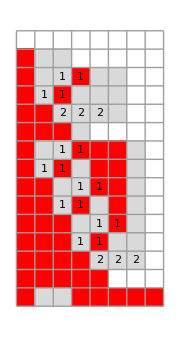
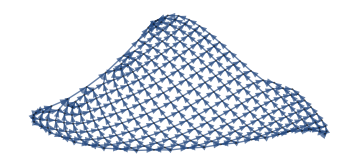
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{2,4,12},{1,2,5},{1,2},{1,5},{6},{1,2,9},{1,2},{2,9},{1,2},{2,9},{1,2},{1,9},{10},{1,2,12},{1,2},{2,12},{1,2},{2,12},{1,2},{2,12},{1,2},{2,12},{1,33},{12,14},{1,2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{2,15},{1,2},{1,15},{16},{1,2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{2,19},{1,2},{1,19},{20},{1,2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,2},{2,22},{1,53},{22,24},{1,2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{1,25},{26},{1,2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{1,29},{30},{1,2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,73},{32,34},{1,2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{2,35},{1,2},{1,35},{36},{1,2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2,39},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{1},{},{1,2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2}}

{{2,4,12},{1,2,5},{1,2},{1,5},{6},{1,2,9},2·{{1,2},{2,9}},{1,2},{1,9},{10},{1,2,12},4·{{1,2},{2,12}},{1,33},{12,14},{1,2,15},5·{{1,2},{2,15}},{1,2},{1,15},{16},{1,2,19},7·{{1,2},{2,19}},{1,2},{1,19},{20},{1,2,22},9·{{1,2},{2,22}},{1,53},{22,24},{1,2,25},10·{{1,2},{2,25}},{1,2},{1,25},{26},{1,2,29},12·{{1,2},{2,29}},{1,2},{1,29},{30},{1,2,32},14·{{1,2},{2,32}},{1,73},{32,34},{1,2,35},15·{{1,2},{2,35}},{1,2},{1,35},{36},{1,2,39},8·{{1,2},{2,39}},9·{{1,2},{2}},{1,2},{1},{},2·{{1,2}},7·{{2},{1,2}}}

{3,3,1,1,2,3,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{{failed,5 | 13 | 38 | 56 | 101 | 129 | 194 | 232
8 | 25 | 18 | 45 | 28 | 65 | 38 | 
17 | -7 | 27 | -17 | 37 | -27 |  | 
-24 | 34 | -44 | 54 | -64 |  |  | 
58 | -78 | 98 | -118 |  |  |  | },{failed,3 | 7 | 26 | 40 | 79 | 103 | 162 | 196
4 | 19 | 14 | 39 | 24 | 59 | 34 | 
15 | -5 | 25 | -15 | 35 | -25 |  | 
-20 | 30 | -40 | 50 | -60 |  |  | 
50 | -70 | 90 | -110 |  |  |  | },{failed,1 | 4 | 9 | 15 | 24 | 34 | 48 | 63
3 | 5 | 6 | 9 | 10 | 14 | 15 | 
2 | 1 | 3 | 1 | 4 | 1 |  | 
-1 | 2 | -2 | 3 | -3 |  |  | 
3 | -4 | 5 | -6 |  |  |  | },{failed,13 | 23 | 56 | 76 | 129 | 159 | 232
10 | 33 | 20 | 53 | 30 | 73 | 
23 | -13 | 33 | -23 | 43 |  | 
-36 | 46 | -56 | 66 |  |  | }}

```mathematica
ssst0=SSS[{"AB"->"BA","AAA"->"B",""->"BAA"},"",250,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6308200640, "QCode" -> "34243233243413", "RuleSet" -> {"AB" -> "BA", "AAA" -> "BB", "" -> "AA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

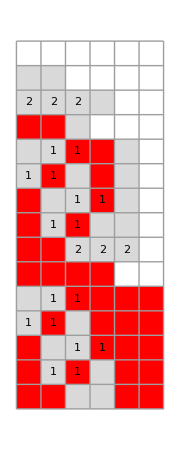
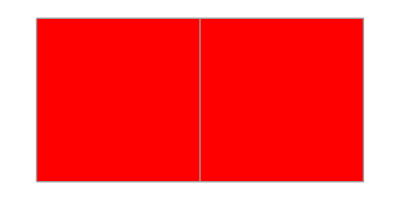
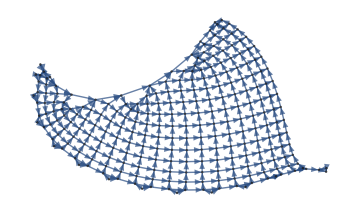
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{2,8},{1,1},{2,4},{1,2},{1,2},{2,5},{1,2},{1,5},{6,8},{1,2},{1,2},{2,8},{1,2},{2,8},{1,2},{2,8},{1,25},{8,10},{1,2},{1,2},{2,9},{1,2},{2,9},{1,2},{2,9},{1,2},{1,9},{10,12},{1,2},{1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,2},{2,13},{1,2},{1,13},{14,16},{1,2},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,2},{2,16},{1,41},{16,18},{1,2},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{2,17},{1,2},{1,17},{18,20},{1,2},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{2,21},{1,2},{1,21},{22,24},{1,2},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,2},{2,24},{1,57},{24,26},{1,2},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{2,25},{1,2},{1,25},{26,28},{1,2},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{2,29},{1,2},{1,29},{30,32},{1,2},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1,2},{2,32},{1},{32,34},{1,2},{1,2},{2,33},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{2},{1,2},{1},{},{1,2},{1}}

{{2,8},{1,1},{2,4},2·{{1,2}},{2,5},{1,2},{1,5},{6,8},2·{{1,2}},2·{{2,8},{1,2}},{2,8},{1,25},{8,10},2·{{1,2}},3·{{2,9},{1,2}},{1,9},{10,12},2·{{1,2}},5·{{2,13},{1,2}},{1,13},{14,16},2·{{1,2}},6·{{2,16},{1,2}},{2,16},{1,41},{16,18},2·{{1,2}},7·{{2,17},{1,2}},{1,17},{18,20},2·{{1,2}},9·{{2,21},{1,2}},{1,21},{22,24},2·{{1,2}},10·{{2,24},{1,2}},{2,24},{1,57},{24,26},2·{{1,2}},11·{{2,25},{1,2}},{1,25},{26,28},2·{{1,2}},13·{{2,29},{1,2}},{1,29},{30,32},2·{{1,2}},14·{{2,32},{1,2}},{2,32},{1},{32,34},2·{{1,2}},{2,33},14·{{1,2},{2}},{1,2},{1},{},{1,2},{1}}

{3,3,2,3,1,1,1,1,2,3,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1}

{{failed,3 | 9 | 28 | 42 | 77 | 99 | 150 | 180 | 247
6 | 19 | 14 | 35 | 22 | 51 | 30 | 67 | 
13 | -5 | 21 | -13 | 29 | -21 | 37 |  | 
-18 | 26 | -34 | 42 | -50 | 58 |  |  | 
44 | -60 | 76 | -92 | 108 |  |  |  | 
-104 | 136 | -168 | 200 |  |  |  |  | },{failed,5 | 20 | 30 | 61 | 79 | 126 | 152 | 215
15 | 10 | 31 | 18 | 47 | 26 | 63 | 
-5 | 21 | -13 | 29 | -21 | 37 |  | 
26 | -34 | 42 | -50 | 58 |  |  | 
-60 | 76 | -92 | 108 |  |  |  | },{failed,1 | 3 | 9 | 15 | 24 | 35 | 49 | 64 | 82
2 | 6 | 6 | 9 | 11 | 14 | 15 | 18 | 
4 | 0 | 3 | 2 | 3 | 1 | 3 |  | 
-4 | 3 | -1 | 1 | -2 | 2 |  |  | 
7 | -4 | 2 | -3 | 4 |  |  |  | 
-11 | 6 | -5 | 7 |  |  |  |  | },{failed,9 | 17 | 42 | 58 | 99 | 123 | 180 | 212
8 | 25 | 16 | 41 | 24 | 57 | 32 | 
17 | -9 | 25 | -17 | 33 | -25 |  | 
-26 | 34 | -42 | 50 | -58 |  |  | 
60 | -76 | 92 | -108 |  |  |  | }}

```mathematica
ssst0=SSS[{"AB"->"BA","AAA"->"BB",""->"AA"},"",250,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6308201251, "QCode" -> "34243233303334", "RuleSet" -> {"AB" -> "BA", "AAAA" -> "", "" -> "AAAB"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

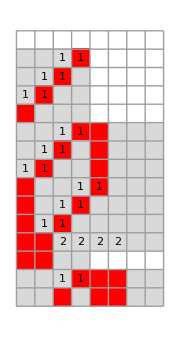
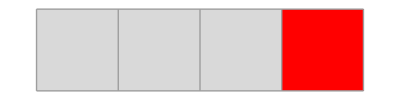
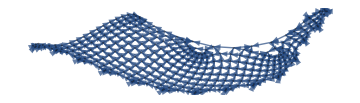
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{1,1,2,3},{1,35},{1,20},{5,8},{1,1,2,3},2·{{1,3}},{3,9},{1,3},{1,2},{1,9},{},{1,1,2,3},2·{{1,3}},{3,12},2·{{1,3}},{3,12},{1,3},{1,2},{1,12},{},{1,1,2,3},2·{{1,3}},{3,15},2·{{1,3}},{3,15},2·{{1,3}},{3,15},{1,3},{1,2},{1,15},{},{1,1,2,3},2·{{1,3}},{3,17},2·{{1,3}},{3,17},2·{{1,3}},{3,17},2·{{1,3}},{3,17},{1,71},{1,44},{17,20},{1,1,2,3},2·{{1,3}},{3,21},2·{{1,3}},{3,21},2·{{1,3}},{3,21},2·{{1,3}},{3,21},2·{{1,3}},{3,21},{1,3},{1,2},{1,21},{},{1,1,2,3},2·{{1,3}},{3,24},2·{{1,3}},{3,24},2·{{1,3}},{3,24},2·{{1,3}},{3,24},2·{{1,3}},{3,24},2·{{1,3}},{3,24},{1,3},{1,2},{1,24},{},{1,1,2,3},2·{{1,3}},{3,27},2·{{1,3}},{3,27},2·{{1,3}},{3,27},2·{{1,3}},{3,27},2·{{1,3}},{3,27},2·{{1,3}},{3,27},2·{{1,3}},{3,27},{1,3},{1,2},{1,27},{},{1,1,2,3},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},2·{{1,3}},{3,29},{1,107},{1,68},{29,32},{1,1,2,3},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},2·{{1,3}},{3,33},{1,3},{1,2},{1,33},{},{1,1,2,3},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},2·{{1,3}},{3,36},{1,3},{1,2},{1,36},{},{1,1,2,3},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},2·{{1,3}},{3,39},{1,3},{1,2},{1,39},{},{1,1,2,3},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1,3}},{3,41},2·{{1}},{41,44},{1,1,2,3},2·{{1,3}},{3,45},2·{{1,3}},{3,45},2·{{1,3}},{3,45},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},{1,3},{1,2},{1},{},{1,1,2,3},2·{{1,3}},{3},2·{{1,3}},{3},{1,3},{1}}

```mathematica
ssst0=SSS[{"AB"->"BA","AAAA"->"",""->"AAAB"},"",350,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

#### SequenceForm[Association["Index" -> 6308201255, "QCode" -> "34243233303343", "RuleSet" -> {"AB" -> "BA", "AAAA" -> "", "" -> "AABA"}], " : ", {"failed", "failed", "failed", "failed"}, " - ", "OK"]

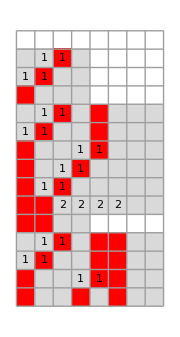
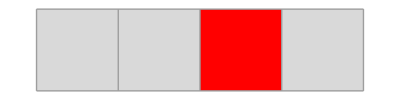
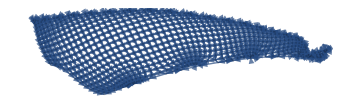
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Part::take: Cannot take positions 645 through 643 in {3,1,1,3,1,1,1,1,1,2,«740»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

{{1,1,2,32},{1,18},{4,7},{1,1,2,3},{1,3},{3,8},{1,3},{1,2},{1,8},{},{1,1,2,3},{1,3},{3,11},2·{{1,3}},{3,11},{1,3},{1,2},{1,11},{},{1,1,2,3},{1,3},{3,14},2·{{1,3}},{3,14},2·{{1,3}},{3,14},{1,3},{1,2},{1,14},{},{1,1,2,3},{1,3},{3,16},2·{{1,3}},{3,16},2·{{1,3}},{3,16},2·{{1,3}},{3,16},{1,68},{1,42},{16,19},{1,1,2,3},{1,3},{3,20},2·{{1,3}},{3,20},2·{{1,3}},{3,20},2·{{1,3}},{3,20},2·{{1,3}},{3,20},{1,3},{1,2},{1,20},{},{1,1,2,3},{1,3},{3,23},2·{{1,3}},{3,23},2·{{1,3}},{3,23},2·{{1,3}},{3,23},2·{{1,3}},{3,23},2·{{1,3}},{3,23},{1,3},{1,2},{1,23},{},{1,1,2,3},{1,3},{3,26},2·{{1,3}},{3,26},2·{{1,3}},{3,26},2·{{1,3}},{3,26},2·{{1,3}},{3,26},2·{{1,3}},{3,26},2·{{1,3}},{3,26},{1,3},{1,2},{1,26},{},{1,1,2,3},{1,3},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},2·{{1,3}},{3,28},{1,104},{1,66},{28,31},{1,1,2,3},{1,3},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},2·{{1,3}},{3,32},{1,3},{1,2},{1,32},{},{1,1,2,3},{1,3},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},2·{{1,3}},{3,35},{1,3},{1,2},{1,35},{},{1,1,2,3},{1,3},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},2·{{1,3}},{3,38},{1,3},{1,2},{1,38},{},{1,1,2,3},{1,3},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},2·{{1,3}},{3,40},{1,140},{1,90},{40,43},{1,1,2,3},{1,3},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},2·{{1,3}},{3,44},{1,3},{1,2},{1,44},{},{1,1,2,3},{1,3},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},2·{{1,3}},{3,47},{1,3},{1,2},{1,47},{},{1,1,2,3},{1,3},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},2·{{1,3}},{3,50},{1,3},{1,2},{1,50},{},{1,1,2,3},{1,3},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},2·{{1,3}},{3,52},{1,176},{1,114},{52,55},{1,1,2,3},{1,3},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},2·{{1,3}},{3,56},{1,3},{1,2},{1,56},{},{1,1,2,3},{1,3},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},2·{{1,3}},{3,59},{1,3},{1,2},{1,59},{},{1,1,2,3},{1,3},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},2·{{1,3}},{3,62},{1,3},{1,2},{1,62},{},{1,1,2,3},{1,3},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3,64},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1}},{},{1,1,2,3},{1,3},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1,3}},{3},2·{{1}}}

{3,1,1,3,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ssst0=SSS[{"AB"->"BA","AAAA"->"",""->"AABA"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

#### SequenceForm[Association["Index" -> 6308506375, "QCode" -> "34243323034333", "RuleSet" -> {"AB" -> "BAA", "AA" -> "", "" -> "ABAAA"}], " : ", {"failed", "failed", "3D", "failed"}, " - ", "OK"]

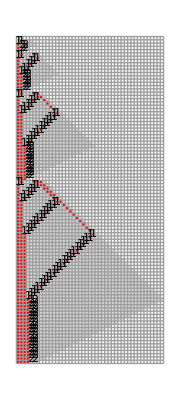
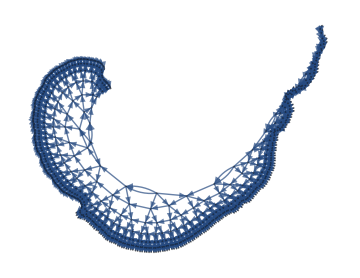
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Part::take: Cannot take positions 16 through 14 in {3,1,2,2,3,1,1,1,1,1,«740»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

{{1,1,3,3},{1,1,5},2·{{}},{1,1,2,3,4},{4,5,13},{1,9,9},{1,7,7},{1,5,5},{1,3,3},{1,1,13},5·{{}},{1,1,2,3,4},{4,5,28},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{9,10,28},{1,19,19},{1,17,17},{1,15,15},{1,13,13},{1,11,11},{1,9,9},{1,7,7},{1,5,5},{1,3,3},{1,1,28},10·{{}},{1,1,2,3,4},{4,5,58},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{9,10,58},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{19,20,58},{1,39,39},{1,37,37},{1,35,35},{1,33,33},{1,31,31},{1,29,29},{1,27,27},{1,25,25},{1,23,23},{1,21,21},{1,19,19},{1,17,17},{1,15,15},{1,13,13},{1,11,11},{1,9,9},{1,7,7},{1,5,5},{1,3,3},{1,1,58},20·{{}},{1,1,2,3,4},{4,5,118},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{9,10,118},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{19,20,118},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{39,40,118},{1,79,79},{1,77,77},{1,75,75},{1,73,73},{1,71,71},{1,69,69},{1,67,67},{1,65,65},{1,63,63},{1,61,61},{1,59,59},{1,57,57},{1,55,55},{1,53,53},{1,51,51},{1,49,49},{1,47,47},{1,45,45},{1,43,43},{1,41,41},{1,39,39},{1,37,37},{1,35,35},{1,33,33},{1,31,31},{1,29,29},{1,27,27},{1,25,25},{1,23,23},{1,21,21},{1,19,19},{1,17,17},{1,15,15},{1,13,13},{1,11,11},{1,9,9},{1,7,7},{1,5,5},{1,3,3},{1,1,118},40·{{}},{1,1,2,3,4},{4,5,238},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{9,10,238},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{19,20,238},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{39,40,238},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{79,80,238},{1,159,159},{1,157,157},{1,155,155},{1,153,153},{1,151,151},{1,149,149},{1,147,147},{1,145,145},{1,143,143},{1,141,141},{1,139,139},{1,137,137},{1,135,135},{1,133,133},{1,131,131},{1,129,129},{1,127,127},{1,125,125},{1,123,123},{1,121,121},{1,119,119},{1,117,117},{1,115,115},{1,113,113},{1,111,111},{1,109,109},{1,107,107},{1,105,105},{1,103,103},{1,101,101},{1,99,99},{1,97,97},{1,95,95},{1,93,93},{1,91,91},{1,89,89},{1,87,87},{1,85,85},{1,83,83},{1,81,81},{1,79,79},{1,77,77},{1,75,75},{1,73,73},{1,71,71},{1,69,69},{1,67,67},{1,65,65},{1,63,63},{1,61,61},{1,59,59},{1,57,57},{1,55,55},{1,53,53},{1,51,51},{1,49,49},{1,47,47},{1,45,45},{1,43,43},{1,41,41},{1,39,39},{1,37,37},{1,35,35},{1,33,33},{1,31,31},{1,29,29},{1,27,27},{1,25,25},{1,23,23},{1,21,21},{1,19,19},{1,17,17},{1,15,15},{1,13,13},{1,11,11},{1,9,9},{1,7,7},{1,5,5},{1,3,3},{1,1,238},80·{{}},{1,1,2,3,4},{4,5},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{1,127,128},{1,128,129},{1,129,130},{1,130,131},{1,131,132},{1,132,133},{1,133,134},{1,134,135},{1,135,136},{1,136,137},{1,137,138},{1,138,139},{1,139,140},{1,140,141},{1,141,142},{1,142,143},{1,143,144},{1,144,145},{1,145,146},{1,146,147},{1,147,148},{1,148,149},{1,149},9·{{1}},{},138·{{1}}}

```mathematica
ssst0=SSS[{"AB"->"BAA","AA"->"",""->"ABAAA"},"",750,SSSSize->Small,SSSMax->100,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

#### SequenceForm[Association["Index" -> 6339856348, "QCode" -> "34324334234231", "RuleSet" -> {"ABA" -> "BAB", "AB" -> "AA", "" -> "A"}], " : ", {"3D", "3D", "failed", "failed"}, " - ", "OK"]

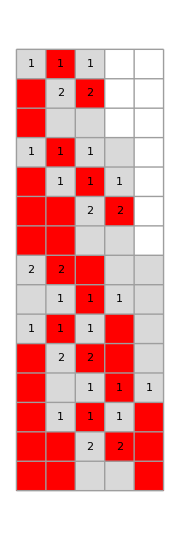
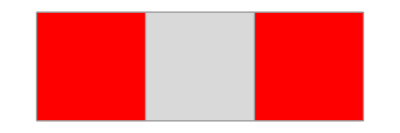
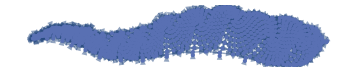
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssst0=SSS[{"ABA"->"BAB","AB"->"AA",""->"A"},"ABA",1000,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

```mathematica
{{"3D",{2,0,12,1},{{3, 7}, {4, 9}, {5, 3}, {-2, 4}},{{3, 7, 16, 28, 47, 71, 104, 144, 195, 255, 328, 412, 511, 623, 752, 896}, {4, 9, 12, 19, 24, 33, 40, 51, 60, 73, 84, 99, 112, 129, 144, }, {5, 3, 7, 5, 9, 7, 11, 9, 13, 11, 15, 13, 17, 15, , }, {-2, 4, -2, 4, -2, 4, -2, 4, -2, 4, -2, 4, -2, , , }}},{"3D",{2,0,11,1},{{4, 8}, {4, 9}, {5, 3}, {-2, 4}},{{4, 8, 17, 29, 48, 72, 105, 145, 196, 256, 329, 413, 512, 624, 753}, {4, 9, 12, 19, 24, 33, 40, 51, 60, 73, 84, 99, 112, 129, }, {5, 3, 7, 5, 9, 7, 11, 9, 13, 11, 15, 13, 17, , }, {-2, 4, -2, 4, -2, 4, -2, 4, -2, 4, -2, 4, , , }}},{"failed"},{"3D",{2,0,11,1},{{4, 10}, {6, 9}, {3, 5}, {2, 0}},{{4, 10, 19, 33, 52, 78, 111, 153, 204, 266, 339, 425, 524, 638, 767, 897}, {6, 9, 14, 19, 26, 33, 42, 51, 62, 73, 86, 99, 114, 129, 130, }, {3, 5, 5, 7, 7, 9, 9, 11, 11, 13, 13, 15, 15, 1, , }, {2, 0, 2, 0, 2, 0, 2, 0, 2, 0, 2, 0, -14, , , }}}}
```

{{1,1,3},{2,3},{1},2·{{1,1,4}},{3,6},{1},{1,2},{1,1,3},{1,1,7},{1,2},{1,1,3},{1,1,5},{1,4},{6,9},{1},{1,2},{1,1,3},{1,1,10},{1,2},{1,1,3},{1,1,8},{1,2},{1,1,3},{1,1,6},{1,5},{9,14},{1},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,15},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,11},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,7},{1,6},{1,10},{14,19},{1},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,20},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,16},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,12},{1,4},{1,2},{1,1,5},{1,1,3},{1,1,8},{1,7},{1,13},{19,26},{1},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,27},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,21},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,15},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,9},{1,8},{1,14},{1,20},{26,33},{1},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,34},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,28},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,22},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,16},{1,6},{1,4},{1,2},{1,1,7},{1,1,5},{1,1,3},{1,1,10},{1,9},{1,17},{1,25},{33,42},{1},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,43},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,35},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,27},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,19},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,11},{1,10},{1,18},{1,26},{1,34},{42,51},{1},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,52},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,44},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,36},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,28},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,20},{1,8},{1,6},{1,4},{1,2},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,12},{1,11},{1,21},{1,31},{1,41},{51,62},{1},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,63},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,53},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,43},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,33},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,23},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,13},{1,12},{1,22},{1,32},{1,42},{1,52},{62,73},{1},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,74},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,64},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,54},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,44},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,34},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,24},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,14},{1,13},{1,25},{1,37},{1,49},{1,61},{73,86},{1},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,87},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,75},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,63},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,51},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,39},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,27},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,15},{1,14},{1,26},{1,38},{1,50},{1,62},{1,74},{86,99},{1},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,100},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,88},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,76},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,64},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,52},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,40},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,28},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,16},{1,15},{1,29},{1,43},{1,57},{1,71},{1,85},{99,114},{1},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,115},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,101},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,87},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,73},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,59},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,45},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,31},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,17},{1,16},{1,30},{1,44},{1,58},{1,72},{1,86},{1,100},{114,129},{1},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,130},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,116},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,102},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,88},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,74},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,60},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,46},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,32},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1,18},{1,17},{1,33},{1,49},{1,65},{1,81},{1,97},{1},{},{1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,17},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,17},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,17},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,17},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},{1,1,17},{1,1,15},{1,1,13},{1,1,11},{1,1,9},{1,1,7},{1,1,5},{1,1,3},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,2},7·{{1,1}},{1,1,3},{1,1},{1}}

### {“ABAA”→”AAAAB”,”A”→”AB”}

```mathematica
ssst0=SSS[{"ABAA"->"AAAAB","A"->"AB"},"AAAAA",500,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ToReducedNetDifferenceSets@ToNetDifferenceSets[Sort@ssst0[["Net"]]]
ssst0["RulesUsed"]
```

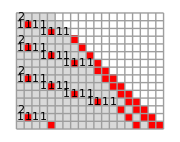
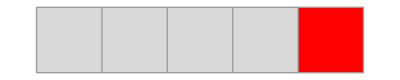
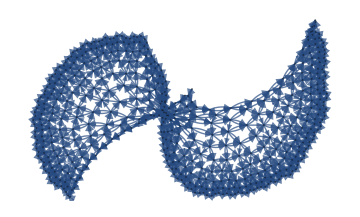
#### " "-Graphics- -Graphics- | "→" | -Graphics- -Graphics- | "→" | -Graphics-"Substitution Rules:"-Graphics-

{{exp,{5,1,4,3/2},4 | 8 | 13 | 20 | 30
4 | 5 | 7 | 10 | 14
1 | 2 | 3 | 4 | 6,1 | 4 | 8 | 13 | 20 | 30 | 44 | 64 | 93 | 136 | 200 | 295 | 437
3 | 4 | 5 | 7 | 10 | 14 | 20 | 29 | 43 | 64 | 95 | 142 | 
1 | 1 | 2 | 3 | 4 | 6 | 9 | 14 | 21 | 31 | 47 |  | },{exp,{5,0,4,3/2},4 | 8 | 13 | 20 | 30
4 | 5 | 7 | 10 | 14
1 | 2 | 3 | 4 | 6,4 | 8 | 13 | 20 | 30 | 44 | 64 | 93 | 136 | 200 | 295 | 437
4 | 5 | 7 | 10 | 14 | 20 | 29 | 43 | 64 | 95 | 142 | 
1 | 2 | 3 | 4 | 6 | 9 | 14 | 21 | 31 | 47 |  | },{exp,{5,2,4,3/2},5 | 9 | 14 | 21 | 31
4 | 5 | 7 | 10 | 14
1 | 2 | 3 | 4 | 6,1 | 2 | 5 | 9 | 14 | 21 | 31 | 45 | 65 | 94 | 137 | 201 | 296
1 | 3 | 4 | 5 | 7 | 10 | 14 | 20 | 29 | 43 | 64 | 95 | 
2 | 1 | 1 | 2 | 3 | 4 | 6 | 9 | 14 | 21 | 31 |  | },{exp,{5,1,4,3/2},5 | 9 | 14 | 21 | 31
4 | 5 | 7 | 10 | 14
1 | 2 | 3 | 4 | 6,2 | 5 | 9 | 14 | 21 | 31 | 45 | 65 | 94 | 137 | 201 | 296
3 | 4 | 5 | 7 | 10 | 14 | 20 | 29 | 43 | 64 | 95 | 
1 | 1 | 2 | 3 | 4 | 6 | 9 | 14 | 21 | 31 |  | }}

{{1,1},{1,1,2,3,3},{3,3,4,4},{1,1},{1,1,3,4,4},{1,1,4,4,5},{4,5,5},{1,1},{1,1,4,5,5},{1,1,5,5,6},{1,1,5,6,6},{6,6,7,7},{1,1},{1,1,6,7,7},{1,1,7,7,8},{1,1,7,8,8},{1,1,8,8,9},{1,1,8,9,9},{9,9,10,10},{1,1},{1,1,9,10,10},{1,1,10,10,11},{1,1,10,11,11},{1,1,11,11,12},{1,1,11,12,12},{1,1,12,12,13},{1,1,12,13,13},{1,1,13,13,14},{13,14,14},{1,1},{1,1,13,14,14},{1,1,14,14,15},{1,1,14,15,15},{1,1,15,15,16},{1,1,15,16,16},{1,1,16,16,17},{1,1,16,17,17},{1,1,17,17,18},{1,1,17,18,18},{1,1,18,18,19},{1,1,18,19,19},{1,1,19,19,20},{19,20,20},{1,1},{1,1,19,20,20},{1,1,20,20,21},{1,1,20,21,21},{1,1,21,21,22},{1,1,21,22,22},{1,1,22,22,23},{1,1,22,23,23},{1,1,23,23,24},{1,1,23,24,24},{1,1,24,24,25},{1,1,24,25,25},{1,1,25,25,26},{1,1,25,26,26},{1,1,26,26,27},{1,1,26,27,27},{1,1,27,27,28},{1,1,27,28,28},{1,1,28,28,29},{28,29,29},{1,1},{1,1,28,29,29},{1,1,29,29,30},{1,1,29,30,30},{1,1,30,30,31},{1,1,30,31,31},{1,1,31,31,32},{1,1,31,32,32},{1,1,32,32,33},{1,1,32,33,33},{1,1,33,33,34},{1,1,33,34,34},{1,1,34,34,35},{1,1,34,35,35},{1,1,35,35,36},{1,1,35,36,36},{1,1,36,36,37},{1,1,36,37,37},{1,1,37,37,38},{1,1,37,38,38},{1,1,38,38,39},{1,1,38,39,39},{1,1,39,39,40},{1,1,39,40,40},{1,1,40,40,41},{1,1,40,41,41},{1,1,41,41,42},{1,1,41,42,42},{42,42,43,43},{1,1},{1,1,42,43,43},{1,1,43,43,44},{1,1,43,44,44},{1,1,44,44,45},{1,1,44,45,45},{1,1,45,45,46},{1,1,45,46,46},{1,1,46,46,47},{1,1,46,47,47},{1,1,47,47,48},{1,1,47,48,48},{1,1,48,48,49},{1,1,48,49,49},{1,1,49,49,50},{1,1,49,50,50},{1,1,50,50,51},{1,1,50,51,51},{1,1,51,51,52},{1,1,51,52,52},{1,1,52,52,53},{1,1,52,53,53},{1,1,53,53,54},{1,1,53,54,54},{1,1,54,54,55},{1,1,54,55,55},{1,1,55,55,56},{1,1,55,56,56},{1,1,56,56,57},{1,1,56,57,57},{1,1,57,57,58},{1,1,57,58,58},{1,1,58,58,59},{1,1,58,59,59},{1,1,59,59,60},{1,1,59,60,60},{1,1,60,60,61},{1,1,60,61,61},{1,1,61,61,62},{1,1,61,62,62},{1,1,62,62,63},{1,1,62,63,63},{63,63,64,64},{1,1},{1,1,63,64,64},{1,1,64,64,65},{1,1,64,65,65},{1,1,65,65,66},{1,1,65,66,66},{1,1,66,66,67},{1,1,66,67,67},{1,1,67,67,68},{1,1,67,68,68},{1,1,68,68,69},{1,1,68,69,69},{1,1,69,69,70},{1,1,69,70,70},{1,1,70,70,71},{1,1,70,71,71},{1,1,71,71,72},{1,1,71,72,72},{1,1,72,72,73},{1,1,72,73,73},{1,1,73,73,74},{1,1,73,74,74},{1,1,74,74,75},{1,1,74,75,75},{1,1,75,75,76},{1,1,75,76,76},{1,1,76,76,77},{1,1,76,77,77},{1,1,77,77,78},{1,1,77,78,78},{1,1,78,78,79},{1,1,78,79,79},{1,1,79,79,80},{1,1,79,80,80},{1,1,80,80,81},{1,1,80,81,81},{1,1,81,81,82},{1,1,81,82,82},{1,1,82,82,83},{1,1,82,83,83},{1,1,83,83,84},{1,1,83,84,84},{1,1,84,84,85},{1,1,84,85,85},{1,1,85,85,86},{1,1,85,86,86},{1,1,86,86,87},{1,1,86,87,87},{1,1,87,87,88},{1,1,87,88,88},{1,1,88,88,89},{1,1,88,89,89},{1,1,89,89,90},{1,1,89,90,90},{1,1,90,90,91},{1,1,90,91,91},{1,1,91,91,92},{1,1,91,92,92},{1,1,92,92,93},{1,1,92,93,93},{1,1,93,93,94},{1,1,93,94,94},{1,1,94,94,95},{94,95,95},{1,1},{1,1,94,95,95},{1,1,95,95,96},{1,1,95,96,96},{1,1,96,96,97},{1,1,96,97,97},{1,1,97,97,98},{1,1,97,98,98},{1,1,98,98,99},{1,1,98,99,99},{1,1,99,99,100},{1,1,99,100,100},{1,1,100,100,101},{1,1,100,101,101},{1,1,101,101,102},{1,1,101,102,102},{1,1,102,102,103},{1,1,102,103,103},{1,1,103,103,104},{1,1,103,104,104},{1,1,104,104,105},{1,1,104,105,105},{1,1,105,105,106},{1,1,105,106,106},{1,1,106,106,107},{1,1,106,107,107},{1,1,107,107,108},{1,1,107,108,108},{1,1,108,108,109},{1,1,108,109,109},{1,1,109,109,110},{1,1,109,110,110},{1,1,110,110,111},{1,1,110,111,111},{1,1,111,111,112},{1,1,111,112,112},{1,1,112,112,113},{1,1,112,113,113},{1,1,113,113,114},{1,1,113,114,114},{1,1,114,114,115},{1,1,114,115,115},{1,1,115,115,116},{1,1,115,116,116},{1,1,116,116,117},{1,1,116,117,117},{1,1,117,117,118},{1,1,117,118,118},{1,1,118,118,119},{1,1,118,119,119},{1,1,119,119,120},{1,1,119,120,120},{1,1,120,120,121},{1,1,120,121,121},{1,1,121,121,122},{1,1,121,122,122},{1,1,122,122,123},{1,1,122,123,123},{1,1,123,123,124},{1,1,123,124,124},{1,1,124,124,125},{1,1,124,125,125},{1,1,125,125,126},{1,1,125,126,126},{1,1,126,126,127},{1,1,126,127,127},{1,1,127,127,128},{1,1,127,128,128},{1,1,128,128,129},{1,1,128,129,129},{1,1,129,129,130},{1,1,129,130,130},{1,1,130,130,131},{1,1,130,131,131},{1,1,131,131,132},{1,1,131,132,132},{1,1,132,132,133},{1,1,132,133,133},{1,1,133,133,134},{1,1,133,134,134},{1,1,134,134,135},{1,1,134,135,135},{1,1,135,135,136},{1,1,135,136,136},{1,1,136,136,137},{1,1,136,137,137},{1,1,137,137,138},{1,1,137,138,138},{1,1,138,138,139},{1,1,138,139,139},{1,1,139,139,140},{1,1,139,140,140},{1,1,140,140,141},{1,1,140,141,141},{141,141,142,142},{1,1},{1,1,141,142,142},{1,1,142,142,143},{1,1,142,143,143},{1,1,143,143,144},{1,1,143,144,144},{1,1,144,144,145},{1,1,144,145,145},{1,1,145,145,146},{1,1,145,146,146},{1,1,146,146,147},{1,1,146,147,147},{1,1,147,147,148},{1,1,147,148,148},{1,1,148,148,149},{1,1,148,149,149},{1,1,149,149,150},{1,1,149,150,150},{1,1,150,150,151},{1,1,150,151,151},{1,1,151,151,152},{1,1,151,152,152},{1,1,152,152,153},{1,1,152,153,153},{1,1,153,153,154},{1,1,153,154,154},{1,1,154,154,155},{1,1,154,155,155},{1,1,155,155,156},{1,1,155,156,156},{1,1,156,156,157},{1,1,156,157,157},{1,1,157,157,158},{1,1,157,158,158},{1,1,158,158,159},{1,1,158,159,159},{1,1,159,159,160},{1,1,159,160,160},{1,1,160,160,161},{1,1,160,161,161},{1,1,161,161,162},{1,1,161,162,162},{1,1,162,162,163},{1,1,162},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}